```mathematica
(* LOAD VARIABLES ----------------------
loads all functions and data (made in this file and evaluated previously) into memory so you don't have to run them again *)
Get[StringReplace[NotebookFileName[],".nb"->", variables.mx"]];
```

```mathematica
(* SAVE VARIABLES ----------------
Save the variables after evaluating them initially so you don't have to re-evaluate them every time *)
DumpSave[StringReplace[NotebookFileName[],".nb"->", variables.mx"],"Global`"];
```

```mathematica
(* ANCILLARY FUNCTIONS -------------------------------------------- *)
```

```mathematica
(* shorten diagonmatrix *)
dm[m_]:=DiagonalMatrix[m];
```

```mathematica
(* Numerical Rounding *)
NR[expr_,tol_]:=N[Round[expr,tol]];
```

```mathematica
(* spherical to carteisan coordinates - useful for parameterizing unit vectors *)
s2c[Φ_,Θ_]:={ Cos[Θ] Sin[Φ], Sin[Φ] Sin[Θ],Cos[Φ]};
(* could have gotten length from the length of Φ or Θ vector, but does not work with FindMaximum because the length of the vector is actually indeterminate until a late step in the evaluation *)
(*s2cvec[Φ_,Θ_,length_]:=Table[s2c[Φ[[i]],Θ[[i]]],{i,length}];*)
(* make it so it can be called with out the superfluous length parameter, which is only needed because of FindMaximum *)
s2cvec[Φ_,Θ_,length_:0]:=Table[s2c[Φ[[i]],Θ[[i]]],{i,If[length==0,Length[Φ],length]}];
```

```mathematica
(* Random Unit vector *)
RR:=RandomReal[NormalDistribution[0,1]];
RUV:=Normalize[{RR,RR,RR}];
```

```mathematica
(* Random Angle and Angle Vector *)
RA:=RandomReal[{0,2 Pi}];
RAV[n_]:=Table[RA,{n}];
```

```mathematica
(* Optimized Initial Angle Vector, with retrospecive values that were found, by trial and error, to converge on the global optimum.
It is called with a minimum of two vectors always, since order 1 has 2 vectors*)
ΦInitAV[n_]:=Table[Pi/2,{n}]; (* start all vectors in xy plane *)
ΘaInitAV[n_]:= Join[Pi{.2,.6},Table[0,{i,n-2}]]; (* make differences .2 Pi and .6 Pi since their cosine are roughly .8 and -.3 *)
ΘbInitAV[n_]:=Pi/2-ΘaInitAV[n]; (* the azimuthal angles for optimized b vectors tend to be Pi/2 minus the angles for av ectors *)
 (* results are close to our optimized values for all tried orders this is sort of cheating but seems will work for higher orders too and always yields a supremum to the Random Angle case*)
```

```mathematica
(* concatenate list to itself m times *)
listPow[list_,m_]:=If[m==1,list,Join[list,listPow[list,m-1]]];
```

```mathematica
(* Join on second dimension and duplicate to match dimensions *)
Join2[pair_,partitionset_]:=Module[{ln},ln=Length[partitionset]; Join[listPow[{{pair}},ln],partitionset,2]];
```

```mathematica
(* "multiply" two sets of indices by keeping any index that is one set but not both ... needed for recursive formula of SuperVector *)
multIndices[a_,b_]:=Complement[a∪b,a∩b];
```

```mathematica
(* DEFINING COEFFICIENT MATRIX ------------------------------------------------ *)
(* It is Hadamard matrix divided by √2, raised to the Nth tensor power. define it recursively. M[N] is 2^N x 2^N *)
(* note initially my definition did not have the factor of 1/2, so the classical values were the power series of 2, 4, 8, 16, etc... 
But this 1/2 factor makes all the classical values 1, for any order, easing comparison with quantum result *)
M[1]={{1,1},{1,-1}}/2;
M[N_]:=KroneckerProduct[M[1],M[N-1]];
```

```mathematica
(* PARTITION FUNCTION ----------------------------------------------------------
Function to find all the parititions of length 2 of a set with even entries 
 It is called by Symmetrization Function *)
(* I could have brute forced this function with Permutations, easier to code, but much longer to calculate and efficiency is important here *)
partitions2[set_]:=Module[{s,out},
s=Length[set];
If[s==2,out={{set}}, 
(* set of partitions should always have depth 4, i.e. 3 indices for partition, pair, element *)
(* loop over i, and Join the partitions from each i and for each join level 2 the pair below ..*)
out={};
Do[
out=Join[out,Join2[{set[[1]],set[[i]]},partitions2[Delete[set,{{1},{i}}]]]];
,{i,2,s}]
];
out
]
```

```mathematica
(* GETCOEFF FUNCTION --------------------------------------------------------------------
takes a matrix of inner products and the list of partitions, returns the coefficient which is equal to replacing each pair in the partitions with the relevant entry from the inner product matrix, then multiplying the elements in each row together, and summing the results to get the coefficient 
Called by Symmetrization function*)
getcoeff[inproducts_,parts_]:=Module[{dim,pair,c},
dim=Dimensions[parts];
c=ConstantArray[1,dim[[1]]];
Do[
pair=parts[[i,j]];
c[[i]]*=inproducts[[pair[[1]],pair[[2]]]];
,{i,dim[[1]]},{j,dim[[2]]}];
Total[c]
]
```

```mathematica
(* SYMMETRIZATION FUNCTION --------------------------------------------------------------------
takes an odd number of unit vectors and returns the symmetrized product 
vecs is a matrix where each row is a unit vector and odd number of rows, 3 columns 
It is called by SuperVector *)
symProd[vecs_,inproducts_,indices_]:= Module[{d,out,parts,factor},
(* e.g. indices = {1,2,4} for a124 or with more precise indexing actual a013 *)
(* vecs are all the primary vectors, inproducts are their inner products, and indices are the relevant indices we want *)
d=Length[indices]; (* d odd *)
out=0;
(* if one vector only no need to symmetrize, output a vector not a set of one vector *)
If[d==1, out=vecs[[indices[[1]]]],
Do[parts=partitions2[Delete[indices,i]];
out+=getcoeff[inproducts,parts] vecs[[indices[[i]]]];
,{i,d}];
(* out/=d!! *)
(* change it to normalized the out vector, to address the shortcoming pointed out by Michael Hall - get nonsensical results *)
Normalize[out]
]
]
```

```mathematica
(* older version which recalculates inner products every time, but is more compact code and more modular since can be called alone if I am interested just in the symmetrized product of any set of odd vectors, I give them to this function 
symProd[vecs_]:= Module[{d,out,range,parts,inproducts,factor},
d=Length[vecs]; (* d odd *)
out=0;
If[d==1, out=vecs[[1]],
(* if one vector only no need to symmetrize *)
range=Range[d];
inproducts=vecs.vecsᵀ;
Do[parts=partitions2[Delete[range,i]];
out+=getcoeff[inproducts,parts] vecs[[i]];
,{i,d}];
out/=d!!
]
] *)
```

```mathematica
(* SUPVECINDICES FUNCTION ------------------------------------------------------------------------------------------------,
creates the indices that are then called by SuperVector, input N, output are 2^N indices 1 to N+1
recursive function *)
SupVecIndices[N_]:=Module[{SuperVecIndlast},
If[N==0,{{1}},
SuperVecIndlast=SupVecIndices[N-1];
Join[SuperVecIndlast,Table[multIndices[{1,N+1},SuperVecIndlast[[i]]],{i,2^(N-1)}]]
]
];
```

```mathematica
(* SUPERVECTOR FUNCTION ------------------------------------------------------------------------------------------------,
takes the primary vector of vectors a, which of length N+1 and each element is a unit vector in 3d, and returns the "SuperVector" A with 2^N elements, with the extra elements being symmetrized products of the elements of a *)
SuperVector[a_]:=Module[{N,Ind,A,inproducts},
N=Length[a]-1;
Ind=SupVecIndices[N];
inproducts=a.aᵀ;
(* symProd could be defined with a[[Ind[[i]]]] alone, but would involve recalculating inner products many times unnecessarily each time it is called, so just evaluate it once and use it *)
Table[symProd[a,inproducts,Ind[[i]]],{i,2^N}]
];
```

```mathematica
(* VALUE FUNCTION  ----------------------------------------------------------------------------------------------------
takes the Subscript[A, N] and Subscript[B, N] to give the value of quantum expression. s=2^N is the length of the supervectors Subscript[A, N] and Subscript[B, N] *)
```

```mathematica
Qvalue[A_,B_,Σ_]:=Module[{s},
s=Length[A];
Total[Table[ A[[i]].Σ.B[[j]],{i,s},{j,s}]*M[Log[2,s]],2]
];
```

```mathematica
(* FIND Q VALUE ------------------------------------------------------
calculates Subscript[A, N] and Subscript[B, N] (which are length 2^N containing many "derived" or product vectors) from a and b (which are just length N, and contain the primary unit vectors)
calculating the derived vectors from the primary ones and putting them in the right order is the hardest part *)
(* Assume input a and b of length N each*)
findQvalue[a_,b_,Σ_]:=Module[{A,B},
A=SuperVector[a];
B=SuperVector[b];
Qvalue[A,B,Σ]
];
```

```mathematica
(* GETMAX ---------------------------------------------------------------
Uses FindMaximum Algorithm to maximize the Qvalue for order N, 
r is weight of random component
Initial Vectors: Option to start iterations with weighted average of randomly selected unit vectors and the optimal ones we "cheated" and optimized in hindsight as close to the optimum. the way to check accuracy is that the optimal vectors provide supremum to all random initials vectors,
call getMax[svalues,N,0] for predetermined initial conditions, and getMax[svalues,N,1] for random initial conditions
for N=6 starts to get slow, few seconds, by N=9 it takes hours .. exponential indeed *)
Clear[Φa,Θa,Φb,Θb];
getMax[svalues_,N_,r_:0]:=Quiet[FindMaximum[findQvalue[s2cvec[Φa,Θa,N+1],s2cvec[Φb,Θb,N+1],dm[svalues]],
{{Φa,r RAV[N+1]+(1-r)ΦInitAV[N+1]},{Θa,r RAV[N+1]+(1-r)ΘaInitAV[N+1]},
{Φb,r RAV[N+1]+(1-r)ΦInitAV[N+1]},{Θb,r RAV[N+1]+(1-r)ΘbInitAV[N+1]}},
AccuracyGoal->6,PrecisionGoal->6, MaxIterations->1000]];
```

```mathematica
(* Define function to check frequency of times it gets various local maxima using the random start vector, we want it to be accurate in the sense of getting the global maximum as frequently as possible *)
(* For a single order *)
CheckAccuracy[svalues_,order_,ntrials_]:=Tally[NR[Table[getMax[svalues,order,1][[1]],{ntrials}],10^-4]];
(* For all orders up till maxrder *)
CheckAccuracyTable[svalues_,maxorder_,ntrials_]:= Table[CheckAccuracy[{1,1,1},i,ntrials],{i,maxorder}];
```

```mathematica
(* GET VECTORS ----------------------------------
Take the output ofthe optimization algorithm getMax , which is in association form for spherical coordinate angles, and return the cartesian vectors and their inner products *)
getVectors[out_,getSuperVectors_:False]:=Module[{max,a,b,mΦa,mΘa,mΦb,mΘb,tol},
(* rounding tolerance *)
max = out[[1]];
tol=10^-3;
{mΦa,mΘa,mΦb,mΘb}={Φa,Θa,Φb,Θb}/.out[[2]];
(* use Rounding  *)
a=s2cvec[mΦa,mΘa];
b=s2cvec[mΦb,mΘb];
(*output the vectors with their inner products *)
(* defaule outputs megavetors, but option not to *)
NR[If[getSuperVectors,
{max,a,a.aᵀ,SuperVector[a],b,b.bᵀ,SuperVector[b],a.bᵀ},
{max,a,a.aᵀ,b,b.bᵀ,a.bᵀ},
],tol]
]
```

```mathematica
(* DRAW VECTORS -------------------------------- 
takes output of getVectors and draws the optimized vectors for visualization purposes *)
(* colours of the a vectors, only 3 needed since we found that the fourth and higher vectors all equal the third *)
aColour={Red, Green, Blue};
(* colours of the b vectors *)
bColour={Magenta,Yellow,Cyan};
drawVectors[gVout_,hasSuperVectors_:False]:=Module[{aInd,bInd,a,b,aArrows,bArrows},
aInd=2;
bInd=If[hasSuperVectors,5,4]; (* if the gVout was generated with SuperVectors then 4th index, otherwise 5th *)
a=gVout[[aInd]][[All,1;;2]]; (* assumes last index is the "zero" one, that corresponds to the zero singular value *)
b=gVout[[bInd]][[All,1;;2]];
aArrows=Table[{aColour[[i]],Arrow[{{0,0},a[[i]]}]},{i,Min[Length[a],3]}];
bArrows=Table[{bColour[[i]],Arrow[{{0,0},b[[i]]}]},{i,Min[Length[a],3]}];
Graphics[Flatten[{aArrows,bArrows}],ImageSize->Small] (* plot first 3 vectors only, since the rest are just copies of the last one *)
]
```

```mathematica
drawAllVectors[tot_]:=Table[drawVectors[tot[[i]]],{i,Length[tot]}];
```

```mathematica
(* QVALUE SERIES --------------------------------------------------------------------
Quantum and Classical maximum values for rising order *)
(* Quantum - superceded by FullSeries, which runs same code and returns all information, not just the Qvalues *)
QvalueSeries[svalues_,maxorder_,r_:0,tries_:1]:=Table[Max[Table[getMax[svalues,i,r][[1]],{tries}]],{i,maxorder}];
```

```mathematica
(* QVALUE AND VECTORS SERIES 
Returns a series of the QValues and the Vectors that reach that optimal state *)
FullSeries[svalues_,maxorder_,r_:0]:=Table[getVectors[getMax[svalues,i,r],False],{i,maxorder}];
```

```mathematica
(* FullSeries for multiple singular value designations. First SV set to 1, last to 0, middle to fraction sequence *)
MultiSVFullSeries[maxorder_,steps_:5]:=Table[{{1,sv2,0},FullSeries[{1,sv2,0},maxorder]},{sv2,1,0,-1/steps}];
(* MultiSVFullSeries[maxorder_,maxreciprocal_]:=Table[{{1,1/i,0},FullSeries[{1,1/i,0},maxorder]},{i,maxreciprocal}]; *)
```

```mathematica
(* PLOT QValeus SERIES RATIOS ----------------------------------------------------------
Set one SV to 1, one to 0, and the middle one varies, this is completely general since smallest does not matter and largest can be decreased by 
homogeneous scaling of all of them *)
PlotQvalues[maxorder_]:=Plot[QvalueSeries[{1,x,0},maxorder],{x,0,1},PlotStyle->Directive[{Red,Thickness[.0001]}]];
```

```mathematica
(* ------------------------------------------------------------------------------------- *)
```

```mathematica
(* APPLY THE FUNCTIONS TO DIFFERENT THINGS *)
```

```mathematica
(* GLOBAL MAXIMUM AMONG LOCAL MAXIMA --------------------
Run the optimization algorithm many times with random starting vectors, and compare the many local maxima you get. *)
```

```mathematica
(* Interesting findings:
- the number of different local maxima are high for odd orders
- global maximum always most frequent so far but its relative frequency seems to go down as order increases 
- For order 3 and higher the classical bound (of unity) simply does not show up - seems it is not a local maximum or its radius of convergence is very small or perhaps even 0 *)
```

```mathematica
CheckAccuracyTable[{1,1,1},7,100 ]
```

{(1.4142 | 100),(1.5 | 98
1. | 2),(1.4322 | 82
1.4176 | 9
1.1053 | 6
1.3222 | 3),(1.4691 | 90
1.1484 | 10),(1.4433 | 66
1.0761 | 8
1.1174 | 11
1.369 | 13
1.1919 | 1
1.051 | 1),(1.4668 | 47
1.4232 | 12
1.1401 | 22
1.076 | 5
1.3402 | 4
1.1167 | 8
1.0319 | 2),(1.3936 | 22
1.4504 | 44
1.0773 | 8
1.3735 | 9
1.0649 | 3
1.0547 | 7
1.0418 | 2
1.0433 | 1
1.0319 | 1
1.0329 | 1
1.0444 | 1
1.0403 | 1)}

```mathematica
(* compare isotropic {1,1,1} case with {1,1,0} case to see if random vectors converge more often in latter ... and they do not *)
CheckAccuracyTable[{1,1,0},7,100]
```

{(1.4142 | 100),(1.5 | 97
1. | 3),(1.4322 | 77
1.1053 | 4
1.4176 | 14
1.3222 | 5),(1.4691 | 91
1.1484 | 9),(1.4433 | 59
1.369 | 21
1.0761 | 5
1.1174 | 14
1.3045 | 1),(1.4668 | 49
1.4232 | 16
1.3402 | 5
1.1401 | 13
1.1167 | 11
1.076 | 4
1.0889 | 1
1.0319 | 1),(1.4504 | 43
1.3735 | 8
1.0773 | 10
1.3936 | 26
1.0403 | 5
1.0649 | 7
1.0319 | 1)}

```mathematica
(* CHECKING RUNTIME --------------------- *)
Table[Timing[FullSeries[{1,1/i,0},j]][[1]],{i,3},{j,7}]
```

(0. | 0. | 0.0312 | 0.0936 | 0.5772 | 4.43043 | 35.00662
0. | 0.0156 | 0.0156 | 0.1092 | 0.624 | 4.58643 | 36.05183
0. | 0. | 0.0312 | 0.0936 | 0.624 | 4.58643 | 35.81783)

```mathematica
Table[Timing[FullSeries[{1,1/i,1/i},j]][[1]],{i,3},{j,7}]
```

(0. | 0.0156 | 0.0156 | 0.1248 | 0.81121 | 6.44284 | 51.26193
0. | 0. | 0.0312 | 0.1404 | 0.85801 | 6.64564 | 52.11993
0. | 0. | 0.0312 | 0.1248 | 0.87361 | 6.58324 | 52.86874)

```mathematica
(* Conclusion: different values for the second singular value don't affect runtime, but convergence is 50% faster when the third SV is zero rather than equal to the second SV (even though both cases yield same maximum) *)
```

```mathematica
(* RUN FULL SERIES up to high order  ----------------------------------------- *)
```

```mathematica
(* After many random tries, found that whenever the global maximum is reached, the output vectors a are coplanar, b are coplanar, each of the two sets has N-1 identical vectors from the total of N +1, and what's more is they have the same indices in a and b sets. the a.aᵀ and b.bᵀ matrices are always identical. but no obvious form for a.bᵀ in general. (seems angles roughly relate by θb= Pi/2 - θa ... that is what I used for initial conditions )
So only 3 unique vectors, one of which is duplicated. 
If v1, v2 are the unique vectors and v3 is the duplicate vector then v1.v2 in the 0.17 to 0.4 range and v1.v3 in 0.75 to 0.85 range and v2.v3 in the -0.3 to -0.4 range .. use this to set the initial angles in ΦInitAV and ΘInitAV to get convergence  always *)
```

```mathematica
(* This runs everything up to order 10 for the multiple values of the second singular value defined in MultiSVFullSeries ... I estimate it would take ~ two days to run ... run it when you have the luxury *)
{t,all}=Timing[MultiSVFullSeries[10]] (* RUN THIS when you can, should take 36 hours or so (35.74 exactly) *)
```

{128665.22557,{{{1,1,0},{{1.414,{{0.924,0.383,0.},{-0.383,0.924,0.}},{{1.,0.},{0.,1.}},{{0.383,0.924,0.},{0.924,-0.383,0.}},{{1.,0.},{0.,1.}},{{0.707,0.707},{0.707,-0.707}}},8,{1.469,4,{{0.967,0.581,0.599,0.599,0.599,0.599,0.599,0.599,0.599,0.599,0.599},9,{0.599,0.961,-0.029,-0.029,3,-0.029,-0.029,-0.029,-0.029}}}}},4,{1}}}
 |  |  |  |

```mathematica
all[[1]]
```

{{1,1,0},(1.414 | (0.924 | 0.383 | 0.
-0.383 | 0.924 | 0.) | (1. | 0.
0. | 1.) | (0.383 | 0.924 | 0.
0.924 | -0.383 | 0.) | (1. | 0.
0. | 1.) | (0.707 | 0.707
0.707 | -0.707)
1.5 | (0.707 | 0.707 | 0.
-0.259 | 0.966 | 0.
0.966 | -0.259 | 0.) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (0.707 | 0.707 | 0.
0.966 | -0.259 | 0.
-0.259 | 0.966 | 0.) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (1. | 0.5 | 0.5
0.5 | -0.5 | 1.
0.5 | 1. | -0.5)
1.432 | (0.866 | 0.5 | 0.
-0.341 | 0.94 | 0.
1. | -0.021 | 0.
1. | -0.021 | 0.) | (1. | 0.175 | 0.855 | 0.855
0.175 | 1. | -0.36 | -0.36
0.855 | -0.36 | 1. | 1.
0.855 | -0.36 | 1. | 1.) | (0.5 | 0.866 | 0.
0.94 | -0.341 | 0.
-0.021 | 1. | 0.
-0.021 | 1. | 0.) | (1. | 0.175 | 0.855 | 0.855
0.175 | 1. | -0.36 | -0.36
0.855 | -0.36 | 1. | 1.
0.855 | -0.36 | 1. | 1.) | (0.866 | 0.644 | 0.481 | 0.481
0.644 | -0.641 | 0.947 | 0.947
0.481 | 0.947 | -0.042 | -0.042
0.481 | 0.947 | -0.042 | -0.042)
1.469 | (0.786 | 0.618 | 0.
-0.293 | 0.956 | 0.
0.997 | -0.081 | 0.
0.997 | -0.081 | 0.
0.997 | -0.081 | 0.) | (1. | 0.361 | 0.734 | 0.734 | 0.734
0.361 | 1. | -0.369 | -0.369 | -0.369
0.734 | -0.369 | 1. | 1. | 1.
0.734 | -0.369 | 1. | 1. | 1.
0.734 | -0.369 | 1. | 1. | 1.) | (0.618 | 0.786 | 0.
0.956 | -0.293 | 0.
-0.081 | 0.997 | 0.
-0.081 | 0.997 | 0.
-0.081 | 0.997 | 0.) | (1. | 0.361 | 0.734 | 0.734 | 0.734
0.361 | 1. | -0.369 | -0.369 | -0.369
0.734 | -0.369 | 1. | 1. | 1.
0.734 | -0.369 | 1. | 1. | 1.
0.734 | -0.369 | 1. | 1. | 1.) | (0.972 | 0.571 | 0.553 | 0.553 | 0.553
0.571 | -0.56 | 0.977 | 0.977 | 0.977
0.553 | 0.977 | -0.161 | -0.161 | -0.161
0.553 | 0.977 | -0.161 | -0.161 | -0.161
0.553 | 0.977 | -0.161 | -0.161 | -0.161)
1.443 | (0.84 | 0.543 | 0.
-0.322 | 0.947 | 0.
1. | -0.008 | 0.
1. | -0.008 | 0.
1. | -0.008 | 0.
1. | -0.008 | 0.) | (1. | 0.244 | 0.836 | 0.836 | 0.836 | 0.836
0.244 | 1. | -0.329 | -0.329 | -0.329 | -0.329
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.) | (0.543 | 0.84 | 0.
0.947 | -0.322 | 0.
-0.008 | 1. | 0.
-0.008 | 1. | 0.
-0.008 | 1. | 0.
-0.008 | 1. | 0.) | (1. | 0.244 | 0.836 | 0.836 | 0.836 | 0.836
0.244 | 1. | -0.329 | -0.329 | -0.329 | -0.329
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.) | (0.912 | 0.621 | 0.536 | 0.536 | 0.536 | 0.536
0.621 | -0.609 | 0.949 | 0.949 | 0.949 | 0.949
0.536 | 0.949 | -0.015 | -0.015 | -0.015 | -0.015
0.536 | 0.949 | -0.015 | -0.015 | -0.015 | -0.015
0.536 | 0.949 | -0.015 | -0.015 | -0.015 | -0.015
0.536 | 0.949 | -0.015 | -0.015 | -0.015 | -0.015)
1.467 | (0.793 | 0.61 | 0.
-0.294 | 0.956 | 0.
0.999 | -0.041 | 0.
0.999 | -0.041 | 0.
0.999 | -0.041 | 0.
0.999 | -0.041 | 0.
0.999 | -0.041 | 0.) | (1. | 0.35 | 0.767 | 0.767 | 0.767 | 0.767 | 0.767
0.35 | 1. | -0.333 | -0.333 | -0.333 | -0.333 | -0.333
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.) | (0.61 | 0.793 | 0.
0.956 | -0.294 | 0.
-0.041 | 0.999 | 0.
-0.041 | 0.999 | 0.
-0.041 | 0.999 | 0.
-0.041 | 0.999 | 0.
-0.041 | 0.999 | 0.) | (1. | 0.35 | 0.767 | 0.767 | 0.767 | 0.767 | 0.767
0.35 | 1. | -0.333 | -0.333 | -0.333 | -0.333 | -0.333
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.) | (0.966 | 0.579 | 0.576 | 0.576 | 0.576 | 0.576 | 0.576
0.579 | -0.562 | 0.967 | 0.967 | 0.967 | 0.967 | 0.967
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083)
1.45 | (0.825 | 0.565 | 0.
-0.311 | 0.951 | 0.
1. | 0. | 0.
1. | 0. | 0.
1. | 0. | 0.
1. | 0. | 0.
1. | 0. | 0.
1. | 0. | 0.) | (1. | 0.281 | 0.825 | 0.825 | 0.825 | 0.825 | 0.825 | 0.825
0.281 | 1. | -0.31 | -0.31 | -0.31 | -0.31 | -0.31 | -0.31
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.565 | 0.825 | 0.
0.951 | -0.311 | 0.
0. | 1. | 0.
0. | 1. | 0.
0. | 1. | 0.
0. | 1. | 0.
0. | 1. | 0.
0. | 1. | 0.) | (1. | 0.281 | 0.825 | 0.825 | 0.825 | 0.825 | 0.825 | 0.825
0.281 | 1. | -0.31 | -0.31 | -0.31 | -0.31 | -0.31 | -0.31
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.933 | 0.609 | 0.565 | 0.565 | 0.565 | 0.565 | 0.565 | 0.565
0.609 | -0.59 | 0.95 | 0.95 | 0.95 | 0.95 | 0.95 | 0.95
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001)
1.467 | (0.793 | 0.609 | 0.
-0.292 | 0.956 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.) | (1. | 0.352 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778
0.352 | 1. | -0.315 | -0.315 | -0.315 | -0.315 | -0.315 | -0.315 | -0.315
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.609 | 0.793 | 0.
0.956 | -0.292 | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.) | (1. | 0.352 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778
0.352 | 1. | -0.315 | -0.315 | -0.315 | -0.315 | -0.315 | -0.315 | -0.315
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.966 | 0.58 | 0.59 | 0.59 | 0.59 | 0.59 | 0.59 | 0.59 | 0.59
0.58 | -0.558 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049)
1.455 | (0.815 | 0.579 | 0.
-0.303 | 0.953 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.) | (1. | 0.305 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818
0.305 | 1. | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.579 | 0.815 | 0.
0.953 | -0.303 | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.) | (1. | 0.305 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818
0.305 | 1. | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.944 | 0.601 | 0.584 | 0.584 | 0.584 | 0.584 | 0.584 | 0.584 | 0.584 | 0.584
0.601 | -0.578 | 0.951 | 0.951 | 0.951 | 0.951 | 0.951 | 0.951 | 0.951 | 0.951
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011)
1.469 | (0.792 | 0.611 | 0.
-0.29 | 0.957 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.) | (1. | 0.355 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783
0.355 | 1. | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.611 | 0.792 | 0.
0.957 | -0.29 | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.) | (1. | 0.355 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783
0.355 | 1. | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.967 | 0.581 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599
0.581 | -0.555 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029))}

```mathematica
all[[2;;4]]
```

({1,4/5,0} | (1.281 | (0.955 | 0.296 | 0.
-0.436 | 0.9 | 0.) | (1. | -0.15
-0.15 | 1.) | (0.477 | 0.879 | 0.
0.945 | -0.328 | 0.) | (1. | 0.162
0.162 | 1.) | (0.716 | 0.805
0.583 | -0.707)
1.356 | (0.898 | 0.44 | 0.
0. | 1. | 0.
0.898 | -0.44 | 0.) | (1. | 0.44 | 0.612
0.44 | 1. | -0.44
0.612 | -0.44 | 1.) | (0.898 | 0.44 | 0.
0.898 | -0.44 | 0.
0. | 1. | 0.) | (1. | 0.612 | 0.44
0.612 | 1. | -0.44
0.44 | -0.44 | 1.) | (1. | 0.612 | 0.44
0.44 | -0.44 | 1.
0.612 | 1. | -0.44)
1.301 | (0.983 | -0.184 | 0.
0.505 | 0.863 | 0.
0.73 | -0.683 | 0.
0.73 | -0.683 | 0.) | (1. | 0.338 | 0.844 | 0.844
0.338 | 1. | -0.221 | -0.221
0.844 | -0.221 | 1. | 1.
0.844 | -0.221 | 1. | 1.) | (0.983 | 0.184 | 0.
0.505 | -0.863 | 0.
0.73 | 0.683 | 0.
0.73 | 0.683 | 0.) | (1. | 0.338 | 0.844 | 0.844
0.338 | 1. | -0.221 | -0.221
0.844 | -0.221 | 1. | 1.
0.844 | -0.221 | 1. | 1.) | (0.932 | 0.656 | 0.592 | 0.592
0.656 | -0.489 | 0.959 | 0.959
0.592 | 0.959 | 0.066 | 0.066
0.592 | 0.959 | 0.066 | 0.066)
1.331 | (0.996 | -0.086 | 0.
0.537 | 0.844 | 0.
0.691 | -0.723 | 0.
0.691 | -0.723 | 0.
0.691 | -0.723 | 0.) | (1. | 0.463 | 0.75 | 0.75 | 0.75
0.463 | 1. | -0.239 | -0.239 | -0.239
0.75 | -0.239 | 1. | 1. | 1.
0.75 | -0.239 | 1. | 1. | 1.
0.75 | -0.239 | 1. | 1. | 1.) | (0.996 | 0.086 | 0.
0.537 | -0.844 | 0.
0.691 | 0.723 | 0.
0.691 | 0.723 | 0.
0.691 | 0.723 | 0.) | (1. | 0.463 | 0.75 | 0.75 | 0.75
0.463 | 1. | -0.239 | -0.239 | -0.239
0.75 | -0.239 | 1. | 1. | 1.
0.75 | -0.239 | 1. | 1. | 1.
0.75 | -0.239 | 1. | 1. | 1.) | (0.985 | 0.607 | 0.627 | 0.627 | 0.626
0.607 | -0.423 | 0.981 | 0.981 | 0.981
0.627 | 0.981 | -0.045 | -0.045 | -0.045
0.627 | 0.981 | -0.045 | -0.045 | -0.045
0.627 | 0.981 | -0.045 | -0.045 | -0.045)
1.312 | (0.99 | -0.14 | 0.
0.523 | 0.852 | 0.
0.738 | -0.675 | 0.
0.738 | -0.675 | 0.
0.738 | -0.675 | 0.
0.738 | -0.675 | 0.) | (1. | 0.399 | 0.825 | 0.825 | 0.825 | 0.825
0.399 | 1. | -0.19 | -0.19 | -0.19 | -0.19
0.825 | -0.19 | 1. | 1. | 1. | 1.
0.825 | -0.19 | 1. | 1. | 1. | 1.
0.825 | -0.19 | 1. | 1. | 1. | 1.
0.825 | -0.19 | 1. | 1. | 1. | 1.) | (0.99 | 0.14 | 0.
0.523 | -0.852 | 0.
0.738 | 0.675 | 0.
0.738 | 0.675 | 0.
0.738 | 0.675 | 0.
0.738 | 0.675 | 0.) | (1. | 0.399 | 0.825 | 0.825 | 0.825 | 0.825
0.399 | 1. | -0.19 | -0.19 | -0.19 | -0.19
0.825 | -0.19 | 1. | 1. | 1. | 1.
0.825 | -0.19 | 1. | 1. | 1. | 1.
0.825 | -0.19 | 1. | 1. | 1. | 1.
0.825 | -0.19 | 1. | 1. | 1. | 1.) | (0.961 | 0.637 | 0.636 | 0.636 | 0.636 | 0.636
0.637 | -0.453 | 0.961 | 0.961 | 0.961 | 0.961
0.636 | 0.961 | 0.088 | 0.088 | 0.088 | 0.088
0.636 | 0.961 | 0.088 | 0.088 | 0.088 | 0.088
0.636 | 0.961 | 0.088 | 0.088 | 0.088 | 0.088
0.636 | 0.961 | 0.088 | 0.088 | 0.088 | 0.088)
1.33 | (0.996 | -0.091 | 0.
0.538 | 0.843 | 0.
0.716 | -0.698 | 0.
0.716 | -0.698 | 0.
0.716 | -0.698 | 0.
0.716 | -0.698 | 0.
0.716 | -0.698 | 0.) | (1. | 0.459 | 0.777 | 0.777 | 0.777 | 0.777 | 0.777
0.459 | 1. | -0.203 | -0.203 | -0.203 | -0.203 | -0.203
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.) | (0.996 | 0.091 | 0.
0.538 | -0.843 | 0.
0.716 | 0.698 | 0.
0.716 | 0.698 | 0.
0.716 | 0.698 | 0.
0.716 | 0.698 | 0.
0.716 | 0.698 | 0.) | (1. | 0.459 | 0.777 | 0.777 | 0.777 | 0.777 | 0.777
0.459 | 1. | -0.203 | -0.203 | -0.203 | -0.203 | -0.203
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.
0.777 | -0.203 | 1. | 1. | 1. | 1. | 1.) | (0.983 | 0.613 | 0.65 | 0.65 | 0.65 | 0.65 | 0.65
0.613 | -0.421 | 0.974 | 0.974 | 0.974 | 0.974 | 0.974
0.65 | 0.974 | 0.026 | 0.026 | 0.026 | 0.026 | 0.026
0.65 | 0.974 | 0.026 | 0.026 | 0.026 | 0.026 | 0.026
0.65 | 0.974 | 0.026 | 0.026 | 0.026 | 0.026 | 0.026
0.65 | 0.974 | 0.026 | 0.026 | 0.026 | 0.026 | 0.026
0.65 | 0.974 | 0.026 | 0.026 | 0.026 | 0.026 | 0.026)
1.319 | (0.993 | -0.118 | 0.
0.532 | 0.847 | 0.
0.742 | -0.671 | 0.
0.742 | -0.671 | 0.
0.742 | -0.671 | 0.
0.742 | -0.671 | 0.
0.742 | -0.671 | 0.
0.742 | -0.671 | 0.) | (1. | 0.429 | 0.815 | 0.815 | 0.815 | 0.815 | 0.815 | 0.815
0.429 | 1. | -0.173 | -0.173 | -0.173 | -0.173 | -0.173 | -0.173
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.993 | 0.118 | 0.
0.532 | -0.847 | 0.
0.742 | 0.671 | 0.
0.742 | 0.671 | 0.
0.742 | 0.671 | 0.
0.742 | 0.671 | 0.
0.742 | 0.671 | 0.
0.742 | 0.671 | 0.) | (1. | 0.429 | 0.815 | 0.815 | 0.815 | 0.815 | 0.815 | 0.815
0.429 | 1. | -0.173 | -0.173 | -0.173 | -0.173 | -0.173 | -0.173
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.
0.815 | -0.173 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.972 | 0.628 | 0.658 | 0.658 | 0.658 | 0.658 | 0.658 | 0.658
0.628 | -0.433 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963
0.658 | 0.963 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.658 | 0.963 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.658 | 0.963 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.658 | 0.963 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.658 | 0.963 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.658 | 0.963 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1)
1.331 | (0.996 | -0.092 | 0.
0.543 | 0.84 | 0.
0.724 | -0.689 | 0.
0.724 | -0.689 | 0.
0.724 | -0.689 | 0.
0.724 | -0.689 | 0.
0.724 | -0.689 | 0.
0.724 | -0.689 | 0.
0.724 | -0.689 | 0.) | (1. | 0.463 | 0.785 | 0.785 | 0.785 | 0.785 | 0.785 | 0.785 | 0.785
0.463 | 1. | -0.185 | -0.185 | -0.185 | -0.185 | -0.185 | -0.185 | -0.185
0.785 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.785 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.785 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.785 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.785 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.785 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.785 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.996 | 0.088 | 0.
0.538 | -0.843 | 0.
0.729 | 0.685 | 0.
0.729 | 0.685 | 0.
0.729 | 0.685 | 0.
0.729 | 0.685 | 0.
0.729 | 0.685 | 0.
0.729 | 0.685 | 0.
0.729 | 0.685 | 0.) | (1. | 0.462 | 0.786 | 0.786 | 0.786 | 0.786 | 0.786 | 0.786 | 0.786
0.462 | 1. | -0.185 | -0.185 | -0.185 | -0.185 | -0.185 | -0.185 | -0.185
0.786 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.786 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.786 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.786 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.786 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.786 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.786 | -0.185 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.984 | 0.613 | 0.663 | 0.663 | 0.663 | 0.663 | 0.663 | 0.663 | 0.663
0.615 | -0.416 | 0.971 | 0.971 | 0.971 | 0.971 | 0.971 | 0.971 | 0.971
0.661 | 0.971 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056
0.661 | 0.971 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056
0.661 | 0.971 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056
0.661 | 0.971 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056
0.661 | 0.971 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056
0.661 | 0.971 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056
0.661 | 0.971 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056 | 0.056)
1.324 | (0.995 | -0.104 | 0.
0.538 | 0.843 | 0.
0.745 | -0.668 | 0.
0.745 | -0.668 | 0.
0.745 | -0.668 | 0.
0.745 | -0.668 | 0.
0.745 | -0.668 | 0.
0.745 | -0.668 | 0.
0.745 | -0.668 | 0.
0.745 | -0.668 | 0.) | (1. | 0.448 | 0.81 | 0.81 | 0.81 | 0.81 | 0.81 | 0.81 | 0.81 | 0.81
0.448 | 1. | -0.162 | -0.162 | -0.162 | -0.162 | -0.162 | -0.162 | -0.162 | -0.162
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.995 | 0.104 | 0.
0.538 | -0.843 | 0.
0.744 | 0.668 | 0.
0.744 | 0.668 | 0.
0.744 | 0.668 | 0.
0.744 | 0.668 | 0.
0.744 | 0.668 | 0.
0.744 | 0.668 | 0.
0.744 | 0.668 | 0.
0.744 | 0.668 | 0.) | (1. | 0.448 | 0.81 | 0.81 | 0.81 | 0.81 | 0.81 | 0.81 | 0.81 | 0.81
0.448 | 1. | -0.162 | -0.162 | -0.162 | -0.162 | -0.162 | -0.162 | -0.162 | -0.162
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | -0.162 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.978 | 0.623 | 0.671 | 0.671 | 0.671 | 0.671 | 0.671 | 0.671 | 0.671 | 0.671
0.623 | -0.421 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963
0.671 | 0.963 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.671 | 0.963 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.671 | 0.963 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.671 | 0.963 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.671 | 0.963 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.671 | 0.963 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.671 | 0.963 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.671 | 0.963 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108)
1.332 | (0.996 | -0.089 | 0.
0.544 | 0.839 | 0.
0.731 | -0.682 | 0.
0.731 | -0.682 | 0.
0.731 | -0.682 | 0.
0.731 | -0.682 | 0.
0.731 | -0.682 | 0.
0.731 | -0.682 | 0.
0.731 | -0.682 | 0.
0.731 | -0.682 | 0.
0.731 | -0.682 | 0.) | (1. | 0.467 | 0.789 | 0.789 | 0.789 | 0.789 | 0.789 | 0.789 | 0.789 | 0.789 | 0.789
0.467 | 1. | -0.174 | -0.174 | -0.174 | -0.174 | -0.174 | -0.174 | -0.174 | -0.174 | -0.174
0.789 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.789 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.789 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.789 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.789 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.789 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.789 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.789 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.789 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.996 | 0.086 | 0.
0.541 | -0.841 | 0.
0.734 | 0.68 | 0.
0.734 | 0.68 | 0.
0.734 | 0.68 | 0.
0.734 | 0.68 | 0.
0.734 | 0.68 | 0.
0.734 | 0.68 | 0.
0.734 | 0.68 | 0.
0.734 | 0.68 | 0.
0.734 | 0.68 | 0.) | (1. | 0.467 | 0.79 | 0.79 | 0.79 | 0.79 | 0.79 | 0.79 | 0.79 | 0.79 | 0.79
0.467 | 1. | -0.174 | -0.174 | -0.174 | -0.174 | -0.174 | -0.174 | -0.174 | -0.174 | -0.174
0.79 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.79 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.79 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.79 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.79 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.79 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.79 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.79 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.79 | -0.174 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.985 | 0.614 | 0.67 | 0.67 | 0.67 | 0.67 | 0.67 | 0.67 | 0.67 | 0.67 | 0.67
0.615 | -0.411 | 0.969 | 0.969 | 0.969 | 0.969 | 0.969 | 0.969 | 0.969 | 0.969 | 0.969
0.67 | 0.969 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073
0.67 | 0.969 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073
0.67 | 0.969 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073
0.67 | 0.969 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073
0.67 | 0.969 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073
0.67 | 0.969 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073
0.67 | 0.969 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073
0.67 | 0.969 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073
0.67 | 0.969 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073 | 0.073))
{1,3/5,0} | (1.166 | (0.979 | 0.204 | 0.
-0.502 | 0.865 | 0.) | (1. | -0.314
-0.314 | 1.) | (0.597 | 0.803 | 0.
0.966 | -0.259 | 0.) | (1. | 0.369
0.369 | 1.) | (0.748 | 0.893
0.395 | -0.708)
1.227 | (0.931 | 0.364 | 0.
0. | 1. | 0.
0.931 | -0.364 | 0.) | (1. | 0.364 | 0.735
0.364 | 1. | -0.364
0.735 | -0.364 | 1.) | (0.931 | 0.364 | 0.
0.931 | -0.364 | 0.
0. | 1. | 0.) | (1. | 0.735 | 0.364
0.735 | 1. | -0.364
0.364 | -0.364 | 1.) | (1. | 0.735 | 0.364
0.364 | -0.364 | 1.
0.735 | 1. | -0.364)
1.188 | (0.994 | -0.11 | 0.
0.603 | 0.797 | 0.
0.773 | -0.635 | 0.
0.773 | -0.635 | 0.) | (1. | 0.512 | 0.838 | 0.838
0.512 | 1. | -0.04 | -0.04
0.838 | -0.04 | 1. | 1.
0.838 | -0.04 | 1. | 1.) | (0.994 | 0.11 | 0.
0.603 | -0.797 | 0.
0.773 | 0.635 | 0.
0.773 | 0.635 | 0.) | (1. | 0.512 | 0.838 | 0.838
0.512 | 1. | -0.04 | -0.04
0.838 | -0.04 | 1. | 1.
0.838 | -0.04 | 1. | 1.) | (0.976 | 0.687 | 0.698 | 0.698
0.687 | -0.272 | 0.972 | 0.972
0.698 | 0.972 | 0.195 | 0.195
0.698 | 0.972 | 0.195 | 0.195)
1.209 | (0.978 | 0.209 | 0.
0.106 | 0.994 | 0.
0.956 | -0.292 | 0.
0.956 | -0.292 | 0.
0.956 | -0.292 | 0.) | (1. | 0.312 | 0.874 | 0.874 | 0.874
0.312 | 1. | -0.188 | -0.188 | -0.188
0.874 | -0.188 | 1. | 1. | 1.
0.874 | -0.188 | 1. | 1. | 1.
0.874 | -0.188 | 1. | 1. | 1.) | (0.942 | 0.335 | 0.
0.895 | -0.446 | 0.
0.282 | 0.959 | 0.
0.282 | 0.959 | 0.
0.282 | 0.959 | 0.) | (1. | 0.694 | 0.587 | 0.587 | 0.587
0.694 | 1. | -0.176 | -0.176 | -0.176
0.587 | -0.176 | 1. | 1. | 1.
0.587 | -0.176 | 1. | 1. | 1.
0.587 | -0.176 | 1. | 1. | 1.) | (0.991 | 0.782 | 0.477 | 0.477 | 0.477
0.433 | -0.349 | 0.984 | 0.984 | 0.984
0.804 | 0.986 | -0.01 | -0.01 | -0.01
0.804 | 0.986 | -0.01 | -0.01 | -0.01
0.804 | 0.986 | -0.01 | -0.01 | -0.01)
1.198 | (0.997 | -0.075 | 0.
0.617 | 0.787 | 0.
0.778 | -0.629 | 0.
0.778 | -0.629 | 0.
0.778 | -0.629 | 0.
0.778 | -0.629 | 0.) | (1. | 0.556 | 0.823 | 0.823 | 0.823 | 0.823
0.556 | 1. | -0.015 | -0.015 | -0.015 | -0.015
0.823 | -0.015 | 1. | 1. | 1. | 1.
0.823 | -0.015 | 1. | 1. | 1. | 1.
0.823 | -0.015 | 1. | 1. | 1. | 1.
0.823 | -0.015 | 1. | 1. | 1. | 1.) | (0.997 | 0.075 | 0.
0.617 | -0.787 | 0.
0.778 | 0.629 | 0.
0.778 | 0.629 | 0.
0.778 | 0.629 | 0.
0.778 | 0.629 | 0.) | (1. | 0.556 | 0.823 | 0.823 | 0.823 | 0.823
0.556 | 1. | -0.015 | -0.015 | -0.015 | -0.015
0.823 | -0.015 | 1. | 1. | 1. | 1.
0.823 | -0.015 | 1. | 1. | 1. | 1.
0.823 | -0.015 | 1. | 1. | 1. | 1.
0.823 | -0.015 | 1. | 1. | 1. | 1.) | (0.989 | 0.675 | 0.728 | 0.728 | 0.728 | 0.728
0.675 | -0.238 | 0.975 | 0.975 | 0.975 | 0.975
0.728 | 0.975 | 0.209 | 0.209 | 0.209 | 0.209
0.728 | 0.975 | 0.209 | 0.209 | 0.209 | 0.209
0.728 | 0.975 | 0.209 | 0.209 | 0.209 | 0.209
0.728 | 0.975 | 0.209 | 0.209 | 0.209 | 0.209)
1.209 | (0.981 | 0.192 | 0.
0.128 | 0.992 | 0.
0.963 | -0.269 | 0.
0.963 | -0.269 | 0.
0.963 | -0.269 | 0.
0.963 | -0.269 | 0.
0.963 | -0.269 | 0.) | (1. | 0.317 | 0.893 | 0.893 | 0.893 | 0.893 | 0.893
0.317 | 1. | -0.143 | -0.143 | -0.143 | -0.143 | -0.143
0.893 | -0.143 | 1. | 1. | 1. | 1. | 1.
0.893 | -0.143 | 1. | 1. | 1. | 1. | 1.
0.893 | -0.143 | 1. | 1. | 1. | 1. | 1.
0.893 | -0.143 | 1. | 1. | 1. | 1. | 1.
0.893 | -0.143 | 1. | 1. | 1. | 1. | 1.) | (0.947 | 0.322 | 0.
0.891 | -0.454 | 0.
0.325 | 0.946 | 0.
0.325 | 0.946 | 0.
0.325 | 0.946 | 0.
0.325 | 0.946 | 0.
0.325 | 0.946 | 0.) | (1. | 0.697 | 0.613 | 0.613 | 0.613 | 0.613 | 0.613
0.697 | 1. | -0.139 | -0.139 | -0.139 | -0.139 | -0.139
0.613 | -0.139 | 1. | 1. | 1. | 1. | 1.
0.613 | -0.139 | 1. | 1. | 1. | 1. | 1.
0.613 | -0.139 | 1. | 1. | 1. | 1. | 1.
0.613 | -0.139 | 1. | 1. | 1. | 1. | 1.
0.613 | -0.139 | 1. | 1. | 1. | 1. | 1.) | (0.991 | 0.787 | 0.501 | 0.501 | 0.501 | 0.501 | 0.501
0.441 | -0.336 | 0.98 | 0.98 | 0.98 | 0.98 | 0.98
0.825 | 0.98 | 0.059 | 0.059 | 0.059 | 0.059 | 0.059
0.825 | 0.98 | 0.059 | 0.059 | 0.059 | 0.059 | 0.059
0.825 | 0.98 | 0.059 | 0.059 | 0.059 | 0.059 | 0.059
0.825 | 0.98 | 0.059 | 0.059 | 0.059 | 0.059 | 0.059
0.825 | 0.98 | 0.059 | 0.059 | 0.059 | 0.059 | 0.059)
1.203 | (0.998 | -0.06 | 0.
0.624 | 0.781 | 0.
0.779 | -0.627 | 0.
0.779 | -0.627 | 0.
0.779 | -0.627 | 0.
0.779 | -0.627 | 0.
0.779 | -0.627 | 0.
0.779 | -0.627 | 0.) | (1. | 0.576 | 0.816 | 0.816 | 0.816 | 0.816 | 0.816 | 0.816
0.576 | 1. | -0.003 | -0.003 | -0.003 | -0.003 | -0.003 | -0.003
0.816 | -0.003 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.003 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.003 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.003 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.003 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.003 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.998 | 0.059 | 0.
0.622 | -0.783 | 0.
0.781 | 0.625 | 0.
0.781 | 0.625 | 0.
0.781 | 0.625 | 0.
0.781 | 0.625 | 0.
0.781 | 0.625 | 0.
0.781 | 0.625 | 0.) | (1. | 0.575 | 0.816 | 0.816 | 0.816 | 0.816 | 0.816 | 0.816
0.575 | 1. | -0.004 | -0.004 | -0.004 | -0.004 | -0.004 | -0.004
0.816 | -0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.816 | -0.004 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.993 | 0.668 | 0.741 | 0.741 | 0.741 | 0.741 | 0.741 | 0.741
0.669 | -0.223 | 0.976 | 0.976 | 0.976 | 0.976 | 0.976 | 0.976
0.741 | 0.976 | 0.216 | 0.217 | 0.217 | 0.217 | 0.217 | 0.217
0.741 | 0.976 | 0.216 | 0.216 | 0.217 | 0.216 | 0.216 | 0.216
0.741 | 0.976 | 0.216 | 0.216 | 0.217 | 0.216 | 0.216 | 0.216
0.741 | 0.976 | 0.216 | 0.217 | 0.217 | 0.217 | 0.217 | 0.217
0.741 | 0.976 | 0.217 | 0.217 | 0.217 | 0.217 | 0.217 | 0.217
0.741 | 0.976 | 0.216 | 0.216 | 0.217 | 0.216 | 0.216 | 0.216)
1.211 | (0.983 | 0.184 | 0.
0.148 | 0.989 | 0.
0.965 | -0.264 | 0.
0.965 | -0.264 | 0.
0.965 | -0.264 | 0.
0.965 | -0.264 | 0.
0.965 | -0.264 | 0.
0.965 | -0.264 | 0.
0.965 | -0.264 | 0.) | (1. | 0.327 | 0.9 | 0.9 | 0.9 | 0.9 | 0.9 | 0.9 | 0.9
0.327 | 1. | -0.118 | -0.118 | -0.118 | -0.118 | -0.118 | -0.118 | -0.118
0.9 | -0.118 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.9 | -0.118 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.9 | -0.118 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.9 | -0.118 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.9 | -0.118 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.9 | -0.118 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.9 | -0.118 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.951 | 0.309 | 0.
0.888 | -0.46 | 0.
0.349 | 0.937 | 0.
0.349 | 0.937 | 0.
0.349 | 0.937 | 0.
0.349 | 0.937 | 0.
0.349 | 0.937 | 0.
0.349 | 0.937 | 0.
0.349 | 0.937 | 0.) | (1. | 0.702 | 0.622 | 0.622 | 0.622 | 0.622 | 0.622 | 0.622 | 0.622
0.702 | 1. | -0.121 | -0.121 | -0.121 | -0.121 | -0.121 | -0.121 | -0.121
0.622 | -0.121 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.622 | -0.121 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.622 | -0.121 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.622 | -0.121 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.622 | -0.121 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.622 | -0.121 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.622 | -0.121 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.992 | 0.788 | 0.515 | 0.515 | 0.515 | 0.515 | 0.515 | 0.515 | 0.515
0.446 | -0.323 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978
0.836 | 0.978 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089
0.836 | 0.978 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089
0.836 | 0.978 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089
0.836 | 0.978 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089
0.836 | 0.978 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089
0.836 | 0.978 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089
0.836 | 0.978 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089 | 0.089)
1.208 | (0.999 | -0.042 | 0.
0.612 | 0.791 | 0.
0.792 | -0.61 | 0.
0.792 | -0.61 | 0.
0.792 | -0.61 | 0.
0.792 | -0.61 | 0.
0.792 | -0.61 | 0.
0.792 | -0.61 | 0.
0.792 | -0.61 | 0.
0.792 | -0.61 | 0.) | (1. | 0.578 | 0.817 | 0.817 | 0.817 | 0.817 | 0.817 | 0.817 | 0.817 | 0.817
0.578 | 1. | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
0.817 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.817 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.817 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.817 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.817 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.817 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.817 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.817 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.998 | 0.06 | 0.
0.641 | -0.768 | 0.
0.77 | 0.638 | 0.
0.77 | 0.638 | 0.
0.77 | 0.638 | 0.
0.77 | 0.638 | 0.
0.77 | 0.638 | 0.
0.77 | 0.638 | 0.
0.77 | 0.638 | 0.
0.77 | 0.638 | 0.) | (1. | 0.594 | 0.806 | 0.806 | 0.806 | 0.806 | 0.806 | 0.806 | 0.806 | 0.806
0.594 | 1. | 0.003 | 0.003 | 0.003 | 0.003 | 0.003 | 0.003 | 0.003 | 0.003
0.806 | 0.003 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.806 | 0.003 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.806 | 0.003 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.806 | 0.003 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.806 | 0.003 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.806 | 0.003 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.806 | 0.003 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.806 | 0.003 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.995 | 0.673 | 0.742 | 0.742 | 0.742 | 0.742 | 0.742 | 0.742 | 0.742 | 0.742
0.658 | -0.215 | 0.976 | 0.976 | 0.976 | 0.976 | 0.976 | 0.976 | 0.976 | 0.976
0.754 | 0.976 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22
0.754 | 0.976 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22
0.754 | 0.976 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22
0.754 | 0.976 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22
0.754 | 0.976 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22
0.754 | 0.976 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22
0.754 | 0.976 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22
0.754 | 0.976 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22 | 0.22)
1.212 | (0.984 | 0.177 | 0.
0.166 | 0.986 | 0.
0.964 | -0.265 | 0.
0.964 | -0.265 | 0.
0.964 | -0.265 | 0.
0.964 | -0.265 | 0.
0.964 | -0.265 | 0.
0.964 | -0.265 | 0.
0.964 | -0.265 | 0.
0.964 | -0.265 | 0.
0.964 | -0.265 | 0.) | (1. | 0.338 | 0.902 | 0.902 | 0.902 | 0.902 | 0.902 | 0.902 | 0.902 | 0.902 | 0.902
0.338 | 1. | -0.101 | -0.101 | -0.101 | -0.101 | -0.101 | -0.101 | -0.101 | -0.101 | -0.101
0.902 | -0.101 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.902 | -0.101 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.902 | -0.101 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.902 | -0.101 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.902 | -0.101 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.902 | -0.101 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.902 | -0.101 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.902 | -0.101 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.902 | -0.101 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.955 | 0.298 | 0.
0.885 | -0.466 | 0.
0.367 | 0.93 | 0.
0.367 | 0.93 | 0.
0.367 | 0.93 | 0.
0.367 | 0.93 | 0.
0.367 | 0.93 | 0.
0.367 | 0.93 | 0.
0.367 | 0.93 | 0.
0.367 | 0.93 | 0.
0.367 | 0.93 | 0.) | (1. | 0.706 | 0.627 | 0.627 | 0.627 | 0.627 | 0.627 | 0.627 | 0.627 | 0.627 | 0.627
0.706 | 1. | -0.108 | -0.108 | -0.108 | -0.108 | -0.108 | -0.108 | -0.108 | -0.108 | -0.108
0.627 | -0.108 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.627 | -0.108 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.627 | -0.108 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.627 | -0.108 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.627 | -0.108 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.627 | -0.108 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.627 | -0.108 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.627 | -0.108 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.627 | -0.108 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.992 | 0.788 | 0.526 | 0.526 | 0.526 | 0.526 | 0.526 | 0.526 | 0.526 | 0.526 | 0.526
0.452 | -0.313 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978 | 0.978
0.842 | 0.977 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.842 | 0.977 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.842 | 0.977 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.842 | 0.977 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.842 | 0.977 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.842 | 0.977 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.842 | 0.977 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.842 | 0.977 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108
0.842 | 0.977 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108 | 0.108))
{1,2/5,0} | (1.077 | (0.993 | 0.115 | 0.
-0.587 | 0.81 | 0.) | (1. | -0.49
-0.49 | 1.) | (0.74 | 0.673 | 0.
0.985 | -0.173 | 0.) | (1. | 0.612
0.612 | 1.) | (0.812 | 0.958
0.111 | -0.718)
1.119 | (0.964 | 0.264 | 0.
0. | 1. | 0.
0.964 | -0.264 | 0.) | (1. | 0.264 | 0.86
0.264 | 1. | -0.264
0.86 | -0.264 | 1.) | (0.964 | 0.264 | 0.
0.964 | -0.264 | 0.
0. | 1. | 0.) | (1. | 0.86 | 0.264
0.86 | 1. | -0.264
0.264 | -0.264 | 1.) | (1. | 0.86 | 0.264
0.264 | -0.264 | 1.
0.86 | 1. | -0.264)
1.097 | (0.998 | 0.059 | 0.
0.277 | 0.961 | 0.
0.968 | -0.252 | 0.
0.968 | -0.252 | 0.) | (1. | 0.334 | 0.951 | 0.951
0.334 | 1. | 0.026 | 0.026
0.951 | 0.026 | 1. | 1.
0.951 | 0.026 | 1. | 1.) | (0.981 | 0.193 | 0.
0.915 | -0.403 | 0.
0.468 | 0.883 | 0.
0.468 | 0.883 | 0.) | (1. | 0.82 | 0.63 | 0.63
0.82 | 1. | 0.072 | 0.072
0.63 | 0.072 | 1. | 1.
0.63 | 0.072 | 1. | 1.) | (0.991 | 0.889 | 0.52 | 0.52
0.457 | -0.134 | 0.979 | 0.979
0.901 | 0.987 | 0.231 | 0.231
0.901 | 0.987 | 0.231 | 0.231)
1.111 | (0.982 | 0.188 | 0.
0.015 | 1. | 0.
0.989 | -0.145 | 0.
0.989 | -0.145 | 0.
0.989 | -0.145 | 0.) | (1. | 0.203 | 0.944 | 0.944 | 0.944
0.203 | 1. | -0.13 | -0.13 | -0.13
0.944 | -0.13 | 1. | 1. | 1.
0.944 | -0.13 | 1. | 1. | 1.
0.944 | -0.13 | 1. | 1. | 1.) | (0.965 | 0.263 | 0.
0.962 | -0.272 | 0.
0.136 | 0.991 | 0.
0.136 | 0.991 | 0.
0.136 | 0.991 | 0.) | (1. | 0.857 | 0.391 | 0.391 | 0.391
0.857 | 1. | -0.139 | -0.139 | -0.139
0.391 | -0.139 | 1. | 1. | 1.
0.391 | -0.139 | 1. | 1. | 1.
0.391 | -0.139 | 1. | 1. | 1.) | (0.997 | 0.894 | 0.319 | 0.319 | 0.319
0.278 | -0.257 | 0.993 | 0.993 | 0.993
0.916 | 0.992 | -0.01 | -0.01 | -0.01
0.916 | 0.992 | -0.01 | -0.01 | -0.01
0.916 | 0.992 | -0.01 | -0.01 | -0.01)
1.105 | (0.995 | 0.097 | 0.
0.212 | 0.977 | 0.
0.979 | -0.202 | 0.
0.979 | -0.202 | 0.
0.979 | -0.202 | 0.
0.979 | -0.202 | 0.) | (1. | 0.306 | 0.955 | 0.955 | 0.955 | 0.955
0.306 | 1. | 0.01 | 0.01 | 0.01 | 0.01
0.955 | 0.01 | 1. | 1. | 1. | 1.
0.955 | 0.01 | 1. | 1. | 1. | 1.
0.955 | 0.01 | 1. | 1. | 1. | 1.
0.955 | 0.01 | 1. | 1. | 1. | 1.) | (0.981 | 0.194 | 0.
0.935 | -0.355 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.) | (1. | 0.848 | 0.566 | 0.566 | 0.566 | 0.566
0.848 | 1. | 0.044 | 0.044 | 0.044 | 0.044
0.566 | 0.044 | 1. | 1. | 1. | 1.
0.566 | 0.044 | 1. | 1. | 1. | 1.
0.566 | 0.044 | 1. | 1. | 1. | 1.
0.566 | 0.044 | 1. | 1. | 1. | 1.) | (0.995 | 0.896 | 0.483 | 0.483 | 0.483 | 0.483
0.397 | -0.149 | 0.981 | 0.981 | 0.981 | 0.981
0.921 | 0.987 | 0.202 | 0.202 | 0.202 | 0.202
0.921 | 0.987 | 0.202 | 0.202 | 0.202 | 0.202
0.921 | 0.987 | 0.202 | 0.202 | 0.202 | 0.202
0.921 | 0.987 | 0.202 | 0.202 | 0.202 | 0.202)
1.112 | (0.985 | 0.175 | 0.
0.031 | 1. | 0.
0.993 | -0.122 | 0.
0.993 | -0.122 | 0.
0.993 | -0.122 | 0.
0.993 | -0.122 | 0.
0.993 | -0.122 | 0.) | (1. | 0.205 | 0.956 | 0.956 | 0.956 | 0.956 | 0.956
0.205 | 1. | -0.091 | -0.091 | -0.091 | -0.091 | -0.091
0.956 | -0.091 | 1. | 1. | 1. | 1. | 1.
0.956 | -0.091 | 1. | 1. | 1. | 1. | 1.
0.956 | -0.091 | 1. | 1. | 1. | 1. | 1.
0.956 | -0.091 | 1. | 1. | 1. | 1. | 1.
0.956 | -0.091 | 1. | 1. | 1. | 1. | 1.) | (0.968 | 0.252 | 0.
0.963 | -0.271 | 0.
0.168 | 0.986 | 0.
0.168 | 0.986 | 0.
0.168 | 0.986 | 0.
0.168 | 0.986 | 0.
0.168 | 0.986 | 0.) | (1. | 0.863 | 0.411 | 0.411 | 0.411 | 0.411 | 0.411
0.863 | 1. | -0.105 | -0.105 | -0.105 | -0.105 | -0.105
0.411 | -0.105 | 1. | 1. | 1. | 1. | 1.
0.411 | -0.105 | 1. | 1. | 1. | 1. | 1.
0.411 | -0.105 | 1. | 1. | 1. | 1. | 1.
0.411 | -0.105 | 1. | 1. | 1. | 1. | 1.
0.411 | -0.105 | 1. | 1. | 1. | 1. | 1.) | (0.997 | 0.9 | 0.338 | 0.338 | 0.338 | 0.338 | 0.338
0.281 | -0.241 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99
0.93 | 0.988 | 0.047 | 0.047 | 0.047 | 0.047 | 0.047
0.93 | 0.988 | 0.047 | 0.047 | 0.047 | 0.047 | 0.047
0.93 | 0.988 | 0.047 | 0.047 | 0.047 | 0.047 | 0.047
0.93 | 0.988 | 0.047 | 0.047 | 0.047 | 0.047 | 0.047
0.93 | 0.988 | 0.047 | 0.047 | 0.047 | 0.047 | 0.047)
1.109 | (0.993 | 0.114 | 0.
0.186 | 0.983 | 0.
0.983 | -0.182 | 0.
0.983 | -0.182 | 0.
0.983 | -0.182 | 0.
0.983 | -0.182 | 0.
0.983 | -0.182 | 0.
0.983 | -0.182 | 0.) | (1. | 0.297 | 0.956 | 0.956 | 0.956 | 0.956 | 0.956 | 0.956
0.297 | 1. | 0.004 | 0.004 | 0.004 | 0.004 | 0.004 | 0.004
0.956 | 0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.956 | 0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.956 | 0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.956 | 0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.956 | 0.004 | 1. | 1. | 1. | 1. | 1. | 1.
0.956 | 0.004 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.981 | 0.193 | 0.
0.942 | -0.335 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.) | (1. | 0.86 | 0.538 | 0.538 | 0.538 | 0.538 | 0.538 | 0.538
0.86 | 1. | 0.032 | 0.032 | 0.032 | 0.032 | 0.032 | 0.032
0.538 | 0.032 | 1. | 1. | 1. | 1. | 1. | 1.
0.538 | 0.032 | 1. | 1. | 1. | 1. | 1. | 1.
0.538 | 0.032 | 1. | 1. | 1. | 1. | 1. | 1.
0.538 | 0.032 | 1. | 1. | 1. | 1. | 1. | 1.
0.538 | 0.032 | 1. | 1. | 1. | 1. | 1. | 1.
0.538 | 0.032 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.997 | 0.898 | 0.469 | 0.469 | 0.469 | 0.469 | 0.469 | 0.469
0.372 | -0.154 | 0.983 | 0.983 | 0.983 | 0.983 | 0.983 | 0.983
0.93 | 0.987 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19
0.93 | 0.987 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19
0.93 | 0.987 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19
0.93 | 0.987 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19
0.93 | 0.987 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19
0.93 | 0.987 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19 | 0.19)
1.114 | (0.986 | 0.17 | 0.
0.042 | 0.999 | 0.
0.994 | -0.113 | 0.
0.994 | -0.113 | 0.
0.994 | -0.113 | 0.
0.994 | -0.113 | 0.
0.994 | -0.113 | 0.
0.994 | -0.113 | 0.
0.994 | -0.113 | 0.) | (1. | 0.211 | 0.96 | 0.96 | 0.96 | 0.96 | 0.96 | 0.96 | 0.96
0.211 | 1. | -0.071 | -0.071 | -0.071 | -0.071 | -0.071 | -0.071 | -0.071
0.96 | -0.071 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.96 | -0.071 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.96 | -0.071 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.96 | -0.071 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.96 | -0.071 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.96 | -0.071 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.96 | -0.071 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.97 | 0.243 | 0.
0.963 | -0.27 | 0.
0.183 | 0.983 | 0.
0.183 | 0.983 | 0.
0.183 | 0.983 | 0.
0.183 | 0.983 | 0.
0.183 | 0.983 | 0.
0.183 | 0.983 | 0.
0.183 | 0.983 | 0.) | (1. | 0.868 | 0.417 | 0.417 | 0.417 | 0.417 | 0.417 | 0.417 | 0.417
0.868 | 1. | -0.089 | -0.089 | -0.089 | -0.089 | -0.089 | -0.089 | -0.089
0.417 | -0.089 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.417 | -0.089 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.417 | -0.089 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.417 | -0.089 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.417 | -0.089 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.417 | -0.089 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.417 | -0.089 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.997 | 0.903 | 0.348 | 0.348 | 0.348 | 0.348 | 0.348 | 0.348 | 0.348
0.284 | -0.23 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99
0.936 | 0.987 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071
0.936 | 0.987 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071
0.936 | 0.987 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071
0.936 | 0.987 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071
0.936 | 0.987 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071
0.936 | 0.987 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071
0.936 | 0.987 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071 | 0.071)
1.112 | (0.992 | 0.123 | 0.
0.174 | 0.985 | 0.
0.985 | -0.172 | 0.
0.985 | -0.172 | 0.
0.985 | -0.172 | 0.
0.985 | -0.172 | 0.
0.985 | -0.172 | 0.
0.985 | -0.172 | 0.
0.985 | -0.172 | 0.
0.985 | -0.172 | 0.) | (1. | 0.293 | 0.957 | 0.957 | 0.957 | 0.957 | 0.957 | 0.957 | 0.957 | 0.957
0.293 | 1. | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002 | 0.002
0.957 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.957 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.957 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.957 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.957 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.957 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.957 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.957 | 0.002 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.981 | 0.192 | 0.
0.946 | -0.325 | 0.
0.35 | 0.937 | 0.
0.35 | 0.937 | 0.
0.35 | 0.937 | 0.
0.35 | 0.937 | 0.
0.35 | 0.937 | 0.
0.35 | 0.937 | 0.
0.35 | 0.937 | 0.
0.35 | 0.937 | 0.) | (1. | 0.866 | 0.524 | 0.524 | 0.524 | 0.524 | 0.524 | 0.524 | 0.524 | 0.524
0.866 | 1. | 0.027 | 0.027 | 0.027 | 0.027 | 0.027 | 0.027 | 0.027 | 0.027
0.524 | 0.027 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.524 | 0.027 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.524 | 0.027 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.524 | 0.027 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.524 | 0.027 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.524 | 0.027 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.524 | 0.027 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.524 | 0.027 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.998 | 0.899 | 0.463 | 0.463 | 0.463 | 0.463 | 0.463 | 0.463 | 0.463 | 0.463
0.36 | -0.156 | 0.983 | 0.983 | 0.983 | 0.983 | 0.983 | 0.983 | 0.983 | 0.983
0.934 | 0.987 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184
0.934 | 0.987 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184
0.934 | 0.987 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184
0.934 | 0.987 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184
0.934 | 0.987 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184
0.934 | 0.987 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184
0.934 | 0.987 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184
0.934 | 0.987 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184 | 0.184)
1.116 | (0.986 | 0.166 | 0.
0.051 | 0.999 | 0.
0.994 | -0.109 | 0.
0.994 | -0.109 | 0.
0.994 | -0.109 | 0.
0.994 | -0.109 | 0.
0.994 | -0.109 | 0.
0.994 | -0.109 | 0.
0.994 | -0.109 | 0.
0.994 | -0.109 | 0.
0.994 | -0.109 | 0.) | (1. | 0.216 | 0.962 | 0.962 | 0.962 | 0.962 | 0.962 | 0.962 | 0.962 | 0.962 | 0.962
0.216 | 1. | -0.058 | -0.058 | -0.058 | -0.058 | -0.058 | -0.058 | -0.058 | -0.058 | -0.058
0.962 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.962 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.962 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.962 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.962 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.962 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.962 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.962 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.962 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.972 | 0.237 | 0.
0.963 | -0.27 | 0.
0.194 | 0.981 | 0.
0.194 | 0.981 | 0.
0.194 | 0.981 | 0.
0.194 | 0.981 | 0.
0.194 | 0.981 | 0.
0.194 | 0.981 | 0.
0.194 | 0.981 | 0.
0.194 | 0.981 | 0.
0.194 | 0.981 | 0.) | (1. | 0.871 | 0.421 | 0.421 | 0.421 | 0.421 | 0.421 | 0.421 | 0.421 | 0.421 | 0.421
0.871 | 1. | -0.078 | -0.078 | -0.078 | -0.078 | -0.078 | -0.078 | -0.078 | -0.078 | -0.078
0.421 | -0.078 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.421 | -0.078 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.421 | -0.078 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.421 | -0.078 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.421 | -0.078 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.421 | -0.078 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.421 | -0.078 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.421 | -0.078 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.421 | -0.078 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.997 | 0.904 | 0.355 | 0.355 | 0.355 | 0.355 | 0.355 | 0.355 | 0.355 | 0.355 | 0.355
0.286 | -0.221 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99
0.94 | 0.987 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086
0.94 | 0.987 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086
0.94 | 0.987 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086
0.94 | 0.987 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086
0.94 | 0.987 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086
0.94 | 0.987 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086
0.94 | 0.987 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086
0.94 | 0.987 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086
0.94 | 0.987 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086 | 0.086)))

```mathematica
all[[5;;6]]
```

({1,1/5,0} | (1.02 | (0.999 | 0.039 | 0.
-0.695 | 0.719 | 0.) | (1. | -0.667
-0.667 | 1.) | (0.895 | 0.446 | 0.
0.997 | -0.08 | 0.) | (1. | 0.856
0.856 | 1.) | (0.912 | 0.993
-0.302 | -0.751)
1.041 | (0.99 | 0.138 | 0.
0. | 1. | 0.
0.99 | -0.138 | 0.) | (1. | 0.138 | 0.962
0.138 | 1. | -0.138
0.962 | -0.138 | 1.) | (0.99 | 0.138 | 0.
0.99 | -0.138 | 0.
0. | 1. | 0.) | (1. | 0.962 | 0.138
0.962 | 1. | -0.138
0.138 | -0.138 | 1.) | (1. | 0.962 | 0.138
0.138 | -0.138 | 1.
0.962 | 1. | -0.138)
1.034 | (0.999 | 0.051 | 0.
0.097 | 0.995 | 0.
0.997 | -0.075 | 0.
0.997 | -0.075 | 0.) | (1. | 0.147 | 0.992 | 0.992
0.147 | 1. | 0.022 | 0.022
0.992 | 0.022 | 1. | 1.
0.992 | 0.022 | 1. | 1.) | (0.993 | 0.122 | 0.
0.987 | -0.163 | 0.
0.227 | 0.974 | 0.
0.227 | 0.974 | 0.) | (1. | 0.959 | 0.344 | 0.344
0.959 | 1. | 0.065 | 0.065
0.344 | 0.065 | 1. | 1.
0.344 | 0.065 | 1. | 1.) | (0.997 | 0.977 | 0.277 | 0.277
0.217 | -0.067 | 0.991 | 0.991
0.981 | 0.996 | 0.153 | 0.153
0.981 | 0.996 | 0.153 | 0.153)
1.041 | (0.994 | 0.109 | 0.
-0.005 | 1. | 0.
0.998 | -0.057 | 0.
0.998 | -0.057 | 0.
0.998 | -0.057 | 0.) | (1. | 0.104 | 0.986 | 0.986 | 0.986
0.104 | 1. | -0.061 | -0.061 | -0.061
0.986 | -0.061 | 1. | 1. | 1.
0.986 | -0.061 | 1. | 1. | 1.
0.986 | -0.061 | 1. | 1. | 1.) | (0.991 | 0.132 | 0.
0.992 | -0.128 | 0.
0.014 | 1. | 0.
0.014 | 1. | 0.
0.014 | 1. | 0.) | (1. | 0.966 | 0.145 | 0.145 | 0.145
0.966 | 1. | -0.115 | -0.115 | -0.115
0.145 | -0.115 | 1. | 1. | 1.
0.145 | -0.115 | 1. | 1. | 1.
0.145 | -0.115 | 1. | 1. | 1.) | (1. | 0.972 | 0.123 | 0.123 | 0.123
0.127 | -0.133 | 1. | 1. | 1.
0.982 | 0.997 | -0.043 | -0.043 | -0.043
0.982 | 0.997 | -0.043 | -0.043 | -0.043
0.982 | 0.997 | -0.043 | -0.043 | -0.043)
1.039 | (0.998 | 0.065 | 0.
0.071 | 0.998 | 0.
0.998 | -0.06 | 0.
0.998 | -0.06 | 0.
0.998 | -0.06 | 0.
0.998 | -0.06 | 0.) | (1. | 0.135 | 0.992 | 0.992 | 0.992 | 0.992
0.135 | 1. | 0.011 | 0.011 | 0.011 | 0.011
0.992 | 0.011 | 1. | 1. | 1. | 1.
0.992 | 0.011 | 1. | 1. | 1. | 1.
0.992 | 0.011 | 1. | 1. | 1. | 1.
0.992 | 0.011 | 1. | 1. | 1. | 1.) | (0.993 | 0.115 | 0.
0.989 | -0.146 | 0.
0.18 | 0.984 | 0.
0.18 | 0.984 | 0.
0.18 | 0.984 | 0.
0.18 | 0.984 | 0.) | (1. | 0.966 | 0.291 | 0.291 | 0.291 | 0.291
0.966 | 1. | 0.034 | 0.034 | 0.034 | 0.034
0.291 | 0.034 | 1. | 1. | 1. | 1.
0.291 | 0.034 | 1. | 1. | 1. | 1.
0.291 | 0.034 | 1. | 1. | 1. | 1.
0.291 | 0.034 | 1. | 1. | 1. | 1.) | (0.999 | 0.978 | 0.243 | 0.243 | 0.243 | 0.243
0.184 | -0.076 | 0.994 | 0.994 | 0.994 | 0.994
0.985 | 0.996 | 0.121 | 0.121 | 0.121 | 0.121
0.985 | 0.996 | 0.121 | 0.121 | 0.121 | 0.121
0.985 | 0.996 | 0.121 | 0.121 | 0.121 | 0.121
0.985 | 0.996 | 0.121 | 0.121 | 0.121 | 0.121)
1.043 | (0.995 | 0.101 | 0.
0.002 | 1. | 0.
0.999 | -0.042 | 0.
0.999 | -0.042 | 0.
0.999 | -0.042 | 0.
0.999 | -0.042 | 0.
0.999 | -0.042 | 0.) | (1. | 0.103 | 0.99 | 0.99 | 0.99 | 0.99 | 0.99
0.103 | 1. | -0.04 | -0.04 | -0.04 | -0.04 | -0.04
0.99 | -0.04 | 1. | 1. | 1. | 1. | 1.
0.99 | -0.04 | 1. | 1. | 1. | 1. | 1.
0.99 | -0.04 | 1. | 1. | 1. | 1. | 1.
0.99 | -0.04 | 1. | 1. | 1. | 1. | 1.
0.99 | -0.04 | 1. | 1. | 1. | 1. | 1.) | (0.992 | 0.126 | 0.
0.992 | -0.125 | 0.
0.04 | 0.999 | 0.
0.04 | 0.999 | 0.
0.04 | 0.999 | 0.
0.04 | 0.999 | 0.
0.04 | 0.999 | 0.) | (1. | 0.969 | 0.165 | 0.165 | 0.165 | 0.165 | 0.165
0.969 | 1. | -0.085 | -0.085 | -0.085 | -0.085 | -0.085
0.165 | -0.085 | 1. | 1. | 1. | 1. | 1.
0.165 | -0.085 | 1. | 1. | 1. | 1. | 1.
0.165 | -0.085 | 1. | 1. | 1. | 1. | 1.
0.165 | -0.085 | 1. | 1. | 1. | 1. | 1.
0.165 | -0.085 | 1. | 1. | 1. | 1. | 1.) | (1. | 0.975 | 0.14 | 0.14 | 0.14 | 0.14 | 0.14
0.127 | -0.123 | 0.999 | 0.999 | 0.999 | 0.999 | 0.999
0.986 | 0.997 | -0.002 | -0.002 | -0.002 | -0.002 | -0.002
0.986 | 0.997 | -0.002 | -0.002 | -0.002 | -0.002 | -0.002
0.986 | 0.997 | -0.002 | -0.002 | -0.002 | -0.002 | -0.002
0.986 | 0.997 | -0.002 | -0.002 | -0.002 | -0.002 | -0.002
0.986 | 0.997 | -0.002 | -0.002 | -0.002 | -0.002 | -0.002)
1.042 | (0.998 | 0.071 | 0.
0.06 | 0.998 | 0.
0.999 | -0.053 | 0.
0.999 | -0.053 | 0.
0.999 | -0.053 | 0.
0.999 | -0.053 | 0.
0.999 | -0.053 | 0.
0.999 | -0.053 | 0.) | (1. | 0.13 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992
0.13 | 1. | 0.007 | 0.007 | 0.007 | 0.007 | 0.007 | 0.007
0.992 | 0.007 | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.007 | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.007 | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.007 | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.007 | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.007 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.994 | 0.111 | 0.
0.99 | -0.139 | 0.
0.162 | 0.987 | 0.
0.162 | 0.987 | 0.
0.162 | 0.987 | 0.
0.162 | 0.987 | 0.
0.162 | 0.987 | 0.
0.161 | 0.987 | 0.) | (1. | 0.969 | 0.27 | 0.27 | 0.27 | 0.27 | 0.27 | 0.27
0.969 | 1. | 0.023 | 0.023 | 0.023 | 0.023 | 0.023 | 0.023
0.27 | 0.023 | 1. | 1. | 1. | 1. | 1. | 1.
0.27 | 0.023 | 1. | 1. | 1. | 1. | 1. | 1.
0.27 | 0.023 | 1. | 1. | 1. | 1. | 1. | 1.
0.27 | 0.023 | 1. | 1. | 1. | 1. | 1. | 1.
0.27 | 0.023 | 1. | 1. | 1. | 1. | 1. | 1.
0.27 | 0.023 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.999 | 0.978 | 0.231 | 0.231 | 0.231 | 0.231 | 0.231 | 0.231
0.171 | -0.079 | 0.995 | 0.995 | 0.995 | 0.995 | 0.995 | 0.995
0.986 | 0.996 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109
0.986 | 0.996 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109
0.986 | 0.996 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109
0.986 | 0.996 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109
0.986 | 0.996 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109
0.986 | 0.996 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109 | 0.109)
1.045 | (0.995 | 0.097 | 0.
0.006 | 1. | 0.
0.999 | -0.036 | 0.
0.999 | -0.036 | 0.
0.999 | -0.036 | 0.
0.999 | -0.036 | 0.
0.999 | -0.036 | 0.
0.999 | -0.036 | 0.
0.999 | -0.036 | 0.) | (1. | 0.104 | 0.991 | 0.991 | 0.991 | 0.991 | 0.991 | 0.991 | 0.991
0.104 | 1. | -0.03 | -0.03 | -0.03 | -0.03 | -0.03 | -0.03 | -0.03
0.991 | -0.03 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.991 | -0.03 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.991 | -0.03 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.991 | -0.03 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.991 | -0.03 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.991 | -0.03 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.991 | -0.03 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.993 | 0.122 | 0.
0.992 | -0.123 | 0.
0.054 | 0.999 | 0.
0.054 | 0.999 | 0.
0.054 | 0.999 | 0.
0.054 | 0.999 | 0.
0.054 | 0.999 | 0.
0.054 | 0.999 | 0.
0.054 | 0.999 | 0.) | (1. | 0.97 | 0.175 | 0.175 | 0.175 | 0.175 | 0.175 | 0.175 | 0.175
0.97 | 1. | -0.069 | -0.069 | -0.069 | -0.069 | -0.069 | -0.069 | -0.069
0.175 | -0.069 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.175 | -0.069 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.175 | -0.069 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.175 | -0.069 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.175 | -0.069 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.175 | -0.069 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.175 | -0.069 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (1. | 0.976 | 0.151 | 0.151 | 0.151 | 0.151 | 0.151 | 0.151 | 0.151
0.128 | -0.116 | 0.999 | 0.999 | 0.999 | 0.999 | 0.999 | 0.999 | 0.999
0.988 | 0.996 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018
0.988 | 0.996 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018
0.988 | 0.996 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018
0.988 | 0.996 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018
0.988 | 0.996 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018
0.988 | 0.996 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018
0.988 | 0.996 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018 | 0.018)
1.044 | (0.997 | 0.074 | 0.
0.055 | 0.998 | 0.
0.999 | -0.05 | 0.
0.999 | -0.05 | 0.
0.999 | -0.05 | 0.
0.999 | -0.05 | 0.
0.999 | -0.05 | 0.
0.999 | -0.05 | 0.
0.999 | -0.05 | 0.
0.999 | -0.05 | 0.) | (1. | 0.129 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992
0.129 | 1. | 0.005 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005 | 0.005
0.992 | 0.005 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.005 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.005 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.005 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.005 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.005 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.005 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | 0.005 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.994 | 0.109 | 0.
0.991 | -0.135 | 0.
0.154 | 0.988 | 0.
0.154 | 0.988 | 0.
0.154 | 0.988 | 0.
0.154 | 0.988 | 0.
0.154 | 0.988 | 0.
0.154 | 0.988 | 0.
0.154 | 0.988 | 0.
0.153 | 0.988 | 0.) | (1. | 0.97 | 0.26 | 0.26 | 0.26 | 0.26 | 0.26 | 0.26 | 0.26 | 0.26
0.97 | 1. | 0.018 | 0.019 | 0.018 | 0.018 | 0.019 | 0.019 | 0.018 | 0.018
0.26 | 0.018 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.26 | 0.019 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.26 | 0.018 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.26 | 0.018 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.26 | 0.019 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.26 | 0.019 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.26 | 0.018 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.26 | 0.018 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.999 | 0.978 | 0.226 | 0.226 | 0.226 | 0.226 | 0.226 | 0.226 | 0.226 | 0.226
0.164 | -0.081 | 0.995 | 0.995 | 0.995 | 0.995 | 0.995 | 0.995 | 0.995 | 0.995
0.987 | 0.996 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104
0.987 | 0.996 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104
0.987 | 0.996 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104
0.987 | 0.996 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104
0.987 | 0.996 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104
0.987 | 0.996 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104
0.987 | 0.996 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104
0.987 | 0.996 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104 | 0.104)
1.046 | (0.996 | 0.095 | 0.
0.01 | 1. | 0.
0.999 | -0.034 | 0.
0.999 | -0.034 | 0.
0.999 | -0.034 | 0.
0.999 | -0.034 | 0.
0.999 | -0.034 | 0.
0.999 | -0.034 | 0.
0.999 | -0.034 | 0.
0.999 | -0.034 | 0.
0.999 | -0.034 | 0.) | (1. | 0.105 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992 | 0.992
0.105 | 1. | -0.024 | -0.024 | -0.024 | -0.024 | -0.024 | -0.024 | -0.024 | -0.024 | -0.024
0.992 | -0.024 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | -0.024 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | -0.024 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | -0.024 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | -0.024 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | -0.024 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | -0.024 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | -0.024 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.992 | -0.024 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.993 | 0.119 | 0.
0.993 | -0.122 | 0.
0.063 | 0.998 | 0.
0.064 | 0.998 | 0.
0.064 | 0.998 | 0.
0.063 | 0.998 | 0.
0.063 | 0.998 | 0.
0.063 | 0.998 | 0.
0.063 | 0.998 | 0.
0.063 | 0.998 | 0.
0.063 | 0.998 | 0.) | (1. | 0.971 | 0.182 | 0.182 | 0.182 | 0.181 | 0.181 | 0.182 | 0.181 | 0.181 | 0.181
0.971 | 1. | -0.058 | -0.058 | -0.058 | -0.058 | -0.058 | -0.058 | -0.059 | -0.059 | -0.059
0.182 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.182 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.182 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.181 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.181 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.182 | -0.058 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.181 | -0.059 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.181 | -0.059 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.181 | -0.059 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (1. | 0.977 | 0.158 | 0.158 | 0.158 | 0.158 | 0.158 | 0.158 | 0.158 | 0.158 | 0.158
0.129 | -0.112 | 0.999 | 0.999 | 0.999 | 0.999 | 0.999 | 0.999 | 0.999 | 0.999 | 0.999
0.988 | 0.996 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03
0.988 | 0.996 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03
0.988 | 0.996 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03
0.988 | 0.996 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03
0.988 | 0.996 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03
0.988 | 0.996 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03
0.988 | 0.996 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03
0.988 | 0.996 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03
0.988 | 0.996 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03 | 0.03))
{1,0,0} | (1. | (1. | 0. | 0.
-0.802 | 0.597 | 0.) | (1. | -0.802
-0.802 | 1.) | (1. | 0. | 0.
1. | 0. | 0.) | (1. | 1.
1. | 1.) | (1. | 1.
-0.802 | -0.802)
1. | (1. | 0. | 0.
-0.698 | 0.717 | 0.
1. | 0. | 0.) | (1. | -0.698 | 1.
-0.698 | 1. | -0.698
1. | -0.698 | 1.) | (1. | 0. | 0.
1. | 0. | 0.
-0.249 | 0.969 | 0.) | (1. | 1. | -0.249
1. | 1. | -0.249
-0.249 | -0.249 | 1.) | (1. | 1. | -0.249
-0.698 | -0.698 | 0.867
1. | 1. | -0.249)
1. | (1. | 0. | 0.
-0.73 | 0.684 | 0.
1. | 0. | 0.
1. | 0. | 0.) | (1. | -0.73 | 1. | 1.
-0.73 | 1. | -0.73 | -0.73
1. | -0.73 | 1. | 1.
1. | -0.73 | 1. | 1.) | (1. | 0. | 0.
1. | 0. | 0.
-0.079 | 0.997 | 0.
-0.079 | 0.997 | 0.) | (1. | 1. | -0.079 | -0.079
1. | 1. | -0.079 | -0.079
-0.079 | -0.079 | 1. | 1.
-0.079 | -0.079 | 1. | 1.) | (1. | 1. | -0.079 | -0.079
-0.73 | -0.73 | 0.739 | 0.739
1. | 1. | -0.079 | -0.079
1. | 1. | -0.079 | -0.079)
1. | (0.998 | 0.062 | 0.
-0.106 | 0.994 | 0.
1. | 0.003 | 0.
1. | 0.003 | 0.
1. | 0.003 | 0.) | (1. | -0.043 | 0.998 | 0.998 | 0.998
-0.043 | 1. | -0.103 | -0.103 | -0.103
0.998 | -0.103 | 1. | 1. | 1.
0.998 | -0.103 | 1. | 1. | 1.
0.998 | -0.103 | 1. | 1. | 1.) | (1. | 0.003 | 0.
1. | 0.001 | 0.
-0.721 | 0.693 | 0.
-0.721 | 0.693 | 0.
-0.721 | 0.693 | 0.) | (1. | 1. | -0.719 | -0.719 | -0.719
1. | 1. | -0.721 | -0.721 | -0.721
-0.719 | -0.721 | 1. | 1. | 1.
-0.719 | -0.721 | 1. | 1. | 1.
-0.719 | -0.721 | 1. | 1. | 1.) | (0.998 | 0.998 | -0.677 | -0.677 | -0.677
-0.102 | -0.105 | 0.765 | 0.765 | 0.765
1. | 1. | -0.719 | -0.719 | -0.719
1. | 1. | -0.719 | -0.719 | -0.719
1. | 1. | -0.719 | -0.719 | -0.719)
1. | (1. | 0.014 | 0.
-0.021 | 1. | 0.
1. | 0.01 | 0.
1. | 0.01 | 0.
1. | 0.01 | 0.
1. | 0.01 | 0.) | (1. | -0.006 | 1. | 1. | 1. | 1.
-0.006 | 1. | -0.011 | -0.011 | -0.011 | -0.011
1. | -0.011 | 1. | 1. | 1. | 1.
1. | -0.011 | 1. | 1. | 1. | 1.
1. | -0.011 | 1. | 1. | 1. | 1.
1. | -0.011 | 1. | 1. | 1. | 1.) | (1. | 0.002 | 0.
1. | 0. | 0.
-0.577 | 0.817 | 0.003
-0.577 | 0.817 | 0.001
-0.575 | 0.818 | 0.003
-0.576 | 0.818 | 0.003) | (1. | 1. | -0.575 | -0.576 | -0.573 | -0.574
1. | 1. | -0.577 | -0.577 | -0.575 | -0.576
-0.575 | -0.577 | 1. | 1. | 1. | 1.
-0.576 | -0.577 | 1. | 1. | 1. | 1.
-0.573 | -0.575 | 1. | 1. | 1. | 1.
-0.574 | -0.576 | 1. | 1. | 1. | 1.) | (1. | 1. | -0.565 | -0.566 | -0.563 | -0.564
-0.018 | -0.021 | 0.829 | 0.828 | 0.83 | 0.829
1. | 1. | -0.569 | -0.569 | -0.567 | -0.568
1. | 1. | -0.569 | -0.569 | -0.567 | -0.568
1. | 1. | -0.569 | -0.569 | -0.567 | -0.568
1. | 1. | -0.569 | -0.569 | -0.567 | -0.568)
1.001 | (0.997 | 0.08 | 0.
-0.133 | 0.991 | -0.001
1. | 0.012 | 0.
1. | 0.012 | 0.
1. | 0.012 | 0.
1. | 0.012 | 0.
1. | 0.012 | 0.) | (1. | -0.054 | 0.998 | 0.998 | 0.998 | 0.998 | 0.998
-0.054 | 1. | -0.121 | -0.121 | -0.121 | -0.121 | -0.121
0.998 | -0.121 | 1. | 1. | 1. | 1. | 1.
0.998 | -0.121 | 1. | 1. | 1. | 1. | 1.
0.998 | -0.121 | 1. | 1. | 1. | 1. | 1.
0.998 | -0.121 | 1. | 1. | 1. | 1. | 1.
0.998 | -0.121 | 1. | 1. | 1. | 1. | 1.) | (1. | 0.006 | 0.
1. | 0. | 0.
-0.698 | 0.716 | 0.
-0.698 | 0.716 | 0.
-0.698 | 0.716 | 0.
-0.698 | 0.716 | 0.
-0.698 | 0.716 | 0.) | (1. | 1. | -0.694 | -0.694 | -0.694 | -0.694 | -0.694
1. | 1. | -0.698 | -0.698 | -0.698 | -0.698 | -0.698
-0.694 | -0.698 | 1. | 1. | 1. | 1. | 1.
-0.694 | -0.698 | 1. | 1. | 1. | 1. | 1.
-0.694 | -0.698 | 1. | 1. | 1. | 1. | 1.
-0.694 | -0.698 | 1. | 1. | 1. | 1. | 1.
-0.694 | -0.698 | 1. | 1. | 1. | 1. | 1.) | (0.997 | 0.997 | -0.639 | -0.639 | -0.639 | -0.639 | -0.639
-0.127 | -0.133 | 0.802 | 0.802 | 0.802 | 0.802 | 0.802
1. | 1. | -0.69 | -0.69 | -0.69 | -0.69 | -0.69
1. | 1. | -0.69 | -0.69 | -0.69 | -0.69 | -0.69
1. | 1. | -0.69 | -0.69 | -0.69 | -0.69 | -0.69
1. | 1. | -0.69 | -0.69 | -0.69 | -0.69 | -0.69
1. | 1. | -0.69 | -0.69 | -0.69 | -0.69 | -0.69)
1. | (1. | 0.026 | 0.
-0.034 | 0.999 | -0.007
1. | 0.018 | 0.
1. | 0.018 | 0.
1. | 0.018 | 0.
1. | 0.018 | 0.
1. | 0.018 | 0.
1. | 0.018 | 0.) | (1. | -0.008 | 1. | 1. | 1. | 1. | 1. | 1.
-0.008 | 1. | -0.016 | -0.016 | -0.016 | -0.016 | -0.016 | -0.016
1. | -0.016 | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.016 | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.016 | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.016 | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.016 | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.016 | 1. | 1. | 1. | 1. | 1. | 1.) | (1. | 0.005 | 0.
1. | 0. | 0.
-0.577 | 0.817 | -0.001
-0.577 | 0.817 | -0.001
-0.576 | 0.817 | 0.
-0.577 | 0.817 | 0.
-0.576 | 0.817 | 0.001
-0.576 | 0.817 | -0.001) | (1. | 1. | -0.573 | -0.573 | -0.572 | -0.573 | -0.572 | -0.573
1. | 1. | -0.577 | -0.577 | -0.576 | -0.577 | -0.576 | -0.577
-0.573 | -0.577 | 1. | 1. | 1. | 1. | 1. | 1.
-0.573 | -0.577 | 1. | 1. | 1. | 1. | 1. | 1.
-0.572 | -0.576 | 1. | 1. | 1. | 1. | 1. | 1.
-0.573 | -0.577 | 1. | 1. | 1. | 1. | 1. | 1.
-0.572 | -0.576 | 1. | 1. | 1. | 1. | 1. | 1.
-0.573 | -0.577 | 1. | 1. | 1. | 1. | 1. | 1.) | (1. | 1. | -0.555 | -0.555 | -0.555 | -0.556 | -0.554 | -0.555
-0.03 | -0.034 | 0.836 | 0.836 | 0.837 | 0.836 | 0.837 | 0.836
1. | 1. | -0.562 | -0.561 | -0.561 | -0.562 | -0.561 | -0.561
1. | 1. | -0.562 | -0.561 | -0.561 | -0.562 | -0.561 | -0.561
1. | 1. | -0.562 | -0.561 | -0.561 | -0.562 | -0.561 | -0.561
1. | 1. | -0.562 | -0.561 | -0.561 | -0.562 | -0.561 | -0.561
1. | 1. | -0.562 | -0.561 | -0.561 | -0.562 | -0.561 | -0.561
1. | 1. | -0.562 | -0.561 | -0.561 | -0.562 | -0.561 | -0.561)
1.001 | (0.996 | 0.087 | 0.
-0.137 | 0.991 | -0.006
1. | 0.021 | 0.
1. | 0.021 | 0.
1. | 0.021 | 0.
1. | 0.021 | 0.
1. | 0.021 | 0.
1. | 0.021 | 0.
1. | 0.021 | 0.) | (1. | -0.05 | 0.998 | 0.998 | 0.998 | 0.998 | 0.998 | 0.998 | 0.998
-0.05 | 1. | -0.116 | -0.116 | -0.116 | -0.116 | -0.116 | -0.116 | -0.116
0.998 | -0.116 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.116 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.116 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.116 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.116 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.116 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.116 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (1. | 0.009 | 0.
1. | 0. | 0.
-0.674 | 0.739 | -0.008
-0.674 | 0.739 | -0.008
-0.673 | 0.739 | -0.009
-0.673 | 0.739 | -0.008
-0.673 | 0.739 | -0.008
-0.673 | 0.739 | -0.009
-0.674 | 0.739 | -0.008) | (1. | 1. | -0.667 | -0.667 | -0.667 | -0.667 | -0.667 | -0.667 | -0.667
1. | 1. | -0.674 | -0.674 | -0.674 | -0.674 | -0.674 | -0.674 | -0.674
-0.667 | -0.674 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.667 | -0.674 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.667 | -0.674 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.667 | -0.674 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.667 | -0.674 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.667 | -0.674 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.667 | -0.674 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.997 | 0.996 | -0.607 | -0.607 | -0.606 | -0.607 | -0.606 | -0.606 | -0.607
-0.128 | -0.137 | 0.824 | 0.824 | 0.824 | 0.824 | 0.824 | 0.824 | 0.824
1. | 1. | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658
1. | 1. | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658
1. | 1. | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658
1. | 1. | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658
1. | 1. | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658
1. | 1. | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658
1. | 1. | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658 | -0.658)
1. | (0.999 | 0.036 | 0.002
-0.045 | 0.997 | 0.055
1. | 0.026 | 0.001
1. | 0.026 | 0.001
1. | 0.026 | 0.001
1. | 0.026 | 0.001
1. | 0.026 | 0.001
1. | 0.026 | 0.001
1. | 0.026 | 0.001
1. | 0.026 | 0.001) | (1. | -0.01 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.01 | 1. | -0.02 | -0.02 | -0.02 | -0.02 | -0.02 | -0.02 | -0.02 | -0.02
1. | -0.02 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.02 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.02 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.02 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.02 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.02 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.02 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.02 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (1. | 0.007 | 0.
1. | -0.001 | 0.
-0.575 | 0.818 | 0.015
-0.579 | 0.815 | 0.018
-0.576 | 0.817 | 0.017
-0.576 | 0.817 | 0.017
-0.577 | 0.817 | 0.012
-0.578 | 0.816 | 0.017
-0.578 | 0.816 | 0.013
-0.578 | 0.816 | 0.015) | (1. | 1. | -0.569 | -0.573 | -0.57 | -0.571 | -0.571 | -0.572 | -0.572 | -0.573
1. | 1. | -0.575 | -0.58 | -0.577 | -0.577 | -0.577 | -0.579 | -0.578 | -0.579
-0.569 | -0.575 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.573 | -0.58 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.57 | -0.577 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.571 | -0.577 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.571 | -0.577 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.572 | -0.579 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.572 | -0.578 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.573 | -0.579 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (1. | 0.999 | -0.545 | -0.55 | -0.547 | -0.547 | -0.547 | -0.549 | -0.548 | -0.549
-0.038 | -0.046 | 0.843 | 0.84 | 0.842 | 0.842 | 0.842 | 0.841 | 0.841 | 0.841
1. | 1. | -0.554 | -0.558 | -0.555 | -0.555 | -0.555 | -0.557 | -0.557 | -0.557
1. | 1. | -0.554 | -0.558 | -0.555 | -0.555 | -0.555 | -0.557 | -0.557 | -0.557
1. | 1. | -0.554 | -0.558 | -0.555 | -0.555 | -0.555 | -0.557 | -0.557 | -0.557
1. | 1. | -0.554 | -0.558 | -0.555 | -0.555 | -0.555 | -0.557 | -0.557 | -0.557
1. | 1. | -0.554 | -0.558 | -0.555 | -0.555 | -0.555 | -0.557 | -0.557 | -0.557
1. | 1. | -0.554 | -0.558 | -0.555 | -0.555 | -0.555 | -0.557 | -0.557 | -0.557
1. | 1. | -0.554 | -0.558 | -0.555 | -0.555 | -0.555 | -0.557 | -0.557 | -0.557
1. | 1. | -0.554 | -0.558 | -0.555 | -0.555 | -0.555 | -0.557 | -0.557 | -0.557)
1.001 | (0.996 | 0.091 | -0.003
-0.133 | 0.99 | -0.038
1. | 0.028 | -0.001
1. | 0.028 | -0.001
1. | 0.028 | -0.001
1. | 0.028 | -0.001
1. | 0.028 | -0.001
1. | 0.028 | -0.001
1. | 0.028 | -0.001
1. | 0.028 | -0.001
1. | 0.028 | -0.001) | (1. | -0.042 | 0.998 | 0.998 | 0.998 | 0.998 | 0.998 | 0.998 | 0.998 | 0.998 | 0.998
-0.042 | 1. | -0.106 | -0.106 | -0.106 | -0.106 | -0.106 | -0.106 | -0.106 | -0.106 | -0.106
0.998 | -0.106 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.106 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.106 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.106 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.106 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.106 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.106 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.106 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.998 | -0.106 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (1. | 0.011 | 0.
1. | -0.001 | 0.
-0.654 | 0.757 | 0.004
-0.653 | 0.757 | 0.004
-0.653 | 0.757 | 0.003
-0.653 | 0.757 | 0.004
-0.653 | 0.757 | 0.003
-0.654 | 0.757 | 0.004
-0.654 | 0.757 | 0.004
-0.654 | 0.757 | 0.005
-0.654 | 0.757 | 0.004) | (1. | 1. | -0.645 | -0.645 | -0.645 | -0.645 | -0.645 | -0.645 | -0.645 | -0.646 | -0.646
1. | 1. | -0.654 | -0.654 | -0.654 | -0.654 | -0.654 | -0.654 | -0.654 | -0.655 | -0.654
-0.645 | -0.654 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.645 | -0.654 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.645 | -0.654 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.645 | -0.654 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.645 | -0.654 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.645 | -0.654 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.645 | -0.654 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.646 | -0.655 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
-0.646 | -0.654 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.997 | 0.996 | -0.582 | -0.581 | -0.581 | -0.581 | -0.581 | -0.582 | -0.582 | -0.582 | -0.582
-0.123 | -0.134 | 0.837 | 0.837 | 0.837 | 0.837 | 0.837 | 0.837 | 0.837 | 0.836 | 0.837
1. | 1. | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.633 | -0.632
1. | 1. | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.633 | -0.632
1. | 1. | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.633 | -0.632
1. | 1. | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.633 | -0.632
1. | 1. | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.633 | -0.632
1. | 1. | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.633 | -0.632
1. | 1. | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.633 | -0.632
1. | 1. | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.633 | -0.632
1. | 1. | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.632 | -0.633 | -0.632)))

```mathematica
(* for {1,x,0} singular values, it is still true (compared to {1,1,0} case) that third vector is duplicated N-1 times and that same indices of this for a and b, but a.aᵀ matrix no longer the same as b.bᵀ *)
```

```mathematica
(* for {1,1,1} Bell states - verify same as {1,1,0} *)
bell=FullSeries[{1,1,1},10]
```

(1.414 | (0.924 | 0.383 | 0.
-0.383 | 0.924 | 0.) | (1. | 0.
0. | 1.) | (0.383 | 0.924 | 0.
0.924 | -0.383 | 0.) | (1. | 0.
0. | 1.) | (0.707 | 0.707
0.707 | -0.707)
1.5 | (0.707 | 0.707 | 0.
-0.259 | 0.966 | 0.
0.966 | -0.259 | 0.) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (0.707 | 0.707 | 0.
0.966 | -0.259 | 0.
-0.259 | 0.966 | 0.) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (1. | 0.5 | 0.5
0.5 | -0.5 | 1.
0.5 | 1. | -0.5)
1.432 | (0.866 | 0.5 | 0.
-0.341 | 0.94 | 0.
1. | -0.021 | 0.
1. | -0.021 | 0.) | (1. | 0.175 | 0.855 | 0.855
0.175 | 1. | -0.36 | -0.36
0.855 | -0.36 | 1. | 1.
0.855 | -0.36 | 1. | 1.) | (0.5 | 0.866 | 0.
0.94 | -0.341 | 0.
-0.021 | 1. | 0.
-0.021 | 1. | 0.) | (1. | 0.175 | 0.855 | 0.855
0.175 | 1. | -0.36 | -0.36
0.855 | -0.36 | 1. | 1.
0.855 | -0.36 | 1. | 1.) | (0.866 | 0.644 | 0.481 | 0.481
0.644 | -0.641 | 0.947 | 0.947
0.481 | 0.947 | -0.042 | -0.042
0.481 | 0.947 | -0.042 | -0.042)
1.469 | (0.786 | 0.618 | 0.
-0.293 | 0.956 | 0.
0.997 | -0.081 | 0.
0.997 | -0.081 | 0.
0.997 | -0.081 | 0.) | (1. | 0.361 | 0.734 | 0.734 | 0.734
0.361 | 1. | -0.369 | -0.369 | -0.369
0.734 | -0.369 | 1. | 1. | 1.
0.734 | -0.369 | 1. | 1. | 1.
0.734 | -0.369 | 1. | 1. | 1.) | (0.618 | 0.786 | 0.
0.956 | -0.293 | 0.
-0.081 | 0.997 | 0.
-0.081 | 0.997 | 0.
-0.081 | 0.997 | 0.) | (1. | 0.361 | 0.734 | 0.734 | 0.734
0.361 | 1. | -0.369 | -0.369 | -0.369
0.734 | -0.369 | 1. | 1. | 1.
0.734 | -0.369 | 1. | 1. | 1.
0.734 | -0.369 | 1. | 1. | 1.) | (0.972 | 0.571 | 0.553 | 0.553 | 0.553
0.571 | -0.56 | 0.977 | 0.977 | 0.977
0.553 | 0.977 | -0.161 | -0.161 | -0.161
0.553 | 0.977 | -0.161 | -0.161 | -0.161
0.553 | 0.977 | -0.161 | -0.161 | -0.161)
1.443 | (0.84 | 0.543 | 0.
-0.322 | 0.947 | 0.
1. | -0.008 | 0.
1. | -0.008 | 0.
1. | -0.008 | 0.
1. | -0.008 | 0.) | (1. | 0.244 | 0.836 | 0.836 | 0.836 | 0.836
0.244 | 1. | -0.329 | -0.329 | -0.329 | -0.329
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.) | (0.543 | 0.84 | 0.
0.947 | -0.322 | 0.
-0.008 | 1. | 0.
-0.008 | 1. | 0.
-0.008 | 1. | 0.
-0.008 | 1. | 0.) | (1. | 0.244 | 0.836 | 0.836 | 0.836 | 0.836
0.244 | 1. | -0.329 | -0.329 | -0.329 | -0.329
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.
0.836 | -0.329 | 1. | 1. | 1. | 1.) | (0.912 | 0.621 | 0.536 | 0.536 | 0.536 | 0.536
0.621 | -0.609 | 0.949 | 0.949 | 0.949 | 0.949
0.536 | 0.949 | -0.015 | -0.015 | -0.015 | -0.015
0.536 | 0.949 | -0.015 | -0.015 | -0.015 | -0.015
0.536 | 0.949 | -0.015 | -0.015 | -0.015 | -0.015
0.536 | 0.949 | -0.015 | -0.015 | -0.015 | -0.015)
1.467 | (0.793 | 0.61 | 0.
-0.294 | 0.956 | 0.
0.999 | -0.041 | 0.
0.999 | -0.041 | 0.
0.999 | -0.041 | 0.
0.999 | -0.041 | 0.
0.999 | -0.041 | 0.) | (1. | 0.35 | 0.767 | 0.767 | 0.767 | 0.767 | 0.767
0.35 | 1. | -0.333 | -0.333 | -0.333 | -0.333 | -0.333
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.) | (0.61 | 0.793 | 0.
0.956 | -0.294 | 0.
-0.041 | 0.999 | 0.
-0.041 | 0.999 | 0.
-0.041 | 0.999 | 0.
-0.041 | 0.999 | 0.
-0.041 | 0.999 | 0.) | (1. | 0.35 | 0.767 | 0.767 | 0.767 | 0.767 | 0.767
0.35 | 1. | -0.333 | -0.333 | -0.333 | -0.333 | -0.333
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.
0.767 | -0.333 | 1. | 1. | 1. | 1. | 1.) | (0.966 | 0.579 | 0.576 | 0.576 | 0.576 | 0.576 | 0.576
0.579 | -0.562 | 0.967 | 0.967 | 0.967 | 0.967 | 0.967
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083
0.576 | 0.967 | -0.083 | -0.083 | -0.083 | -0.083 | -0.083)
1.45 | (0.825 | 0.565 | 0.
-0.311 | 0.951 | 0.
1. | 0. | 0.
1. | 0. | 0.
1. | 0. | 0.
1. | 0. | 0.
1. | 0. | 0.
1. | 0. | 0.) | (1. | 0.281 | 0.825 | 0.825 | 0.825 | 0.825 | 0.825 | 0.825
0.281 | 1. | -0.31 | -0.31 | -0.31 | -0.31 | -0.31 | -0.31
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.565 | 0.825 | 0.
0.951 | -0.311 | 0.
0. | 1. | 0.
0. | 1. | 0.
0. | 1. | 0.
0. | 1. | 0.
0. | 1. | 0.
0. | 1. | 0.) | (1. | 0.281 | 0.825 | 0.825 | 0.825 | 0.825 | 0.825 | 0.825
0.281 | 1. | -0.31 | -0.31 | -0.31 | -0.31 | -0.31 | -0.31
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.
0.825 | -0.31 | 1. | 1. | 1. | 1. | 1. | 1.) | (0.933 | 0.609 | 0.565 | 0.565 | 0.565 | 0.565 | 0.565 | 0.565
0.609 | -0.59 | 0.95 | 0.95 | 0.95 | 0.95 | 0.95 | 0.95
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
0.565 | 0.95 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001)
1.467 | (0.793 | 0.609 | 0.
-0.292 | 0.956 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.
1. | -0.024 | 0.) | (1. | 0.352 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778
0.352 | 1. | -0.315 | -0.315 | -0.315 | -0.315 | -0.315 | -0.315 | -0.315
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.61 | 0.793 | 0.
0.956 | -0.292 | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.
-0.024 | 1. | 0.) | (1. | 0.352 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778 | 0.778
0.352 | 1. | -0.315 | -0.315 | -0.315 | -0.315 | -0.315 | -0.315 | -0.315
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.778 | -0.315 | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.966 | 0.58 | 0.59 | 0.59 | 0.59 | 0.59 | 0.59 | 0.59 | 0.59
0.58 | -0.558 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963 | 0.963
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049
0.59 | 0.963 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049 | -0.049)
1.455 | (0.815 | 0.579 | 0.
-0.303 | 0.953 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.
1. | 0.006 | 0.) | (1. | 0.305 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818
0.305 | 1. | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.579 | 0.815 | 0.
0.953 | -0.303 | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.
0.006 | 1. | 0.) | (1. | 0.305 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818 | 0.818
0.305 | 1. | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298 | -0.298
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.818 | -0.298 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.944 | 0.601 | 0.584 | 0.584 | 0.584 | 0.584 | 0.584 | 0.584 | 0.584 | 0.584
0.601 | -0.578 | 0.951 | 0.951 | 0.951 | 0.951 | 0.951 | 0.951 | 0.951 | 0.951
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011
0.584 | 0.951 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011 | 0.011)
1.469 | (0.792 | 0.611 | 0.
-0.29 | 0.957 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.
1. | -0.015 | 0.) | (1. | 0.355 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783
0.355 | 1. | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.611 | 0.792 | 0.
0.957 | -0.29 | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.
-0.015 | 1. | 0.) | (1. | 0.355 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783 | 0.783
0.355 | 1. | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304 | -0.304
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.783 | -0.304 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.) | (0.967 | 0.581 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599 | 0.599
0.581 | -0.555 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961 | 0.961
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029
0.599 | 0.961 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029 | -0.029))

```mathematica
(* EXTRACT QValue Series from the data above ----------------------------------------- *)
```

```mathematica
(* get q value series for singular values {1,1,0}, same as {1,1,1} *)
q=all[[1,2]][[All,1]]
```

{1.414,1.5,1.432,1.469,1.443,1.467,1.45,1.467,1.455,1.469}

```mathematica
(* q value series for all tried sets of singular values *)
```

```mathematica
qq=all[[All,2]][[All,All,1]]
```

(1.414 | 1.5 | 1.432 | 1.469 | 1.443 | 1.467 | 1.45 | 1.467 | 1.455 | 1.469
1.281 | 1.356 | 1.301 | 1.331 | 1.312 | 1.33 | 1.319 | 1.331 | 1.324 | 1.332
1.166 | 1.227 | 1.188 | 1.209 | 1.198 | 1.209 | 1.203 | 1.211 | 1.208 | 1.212
1.077 | 1.119 | 1.097 | 1.111 | 1.105 | 1.112 | 1.109 | 1.114 | 1.112 | 1.116
1.02 | 1.041 | 1.034 | 1.041 | 1.039 | 1.043 | 1.042 | 1.045 | 1.044 | 1.046
1. | 1. | 1. | 1. | 1. | 1.001 | 1. | 1.001 | 1. | 1.001)

```mathematica
(*so the solution vectors are always coplanar, since only largest two singular values matter ... this is very very odd, what is the fundamental intuitive reason for this? 
may be I need a new type of constraint to get the third singular value,  perhaps symmetrization is the problem. Are other constraint types possible? 
Or may be we actually can get to the order 2 constaint, afterall the Werner type hidden variable theory has one function continuous and the other plus or minus 1. May be to reach the constraint limit, the 2/3, need BOTH to be plus or minus 1 *)
```

```mathematica
(* for small sngular values, in this case {1,1/5,0}, the order 2 is no necessarily the highest, but this I have a very strong suspicion is due to numerical and rounding errors, it is no coincidence that all three orders that give a higher result than order 2 (orders 6,8,10) have 1.001 for singular values {1,0,0} which is impossible as the result is at most 1. So the algorithm increases these higher orders. Probably related to fact that the optimized vectors below for the last row {1,0,0} and higher even orders don't overlap as they are expected to (and do for odd orders) *)
```

```mathematica
(* my hypothesis that the higher orders uniformly converge on some limit, odd ones from below and even ones from above, is falsified by order 8 and 10 q values, but then again that rounding issue may come into play even for larger singular values *)
```

```mathematica
(* DRAW OPTIMAL VECTORS  ------------ for all sv cases *)
```

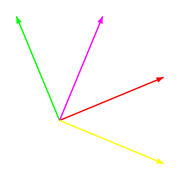
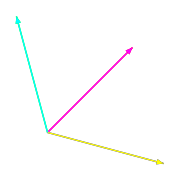
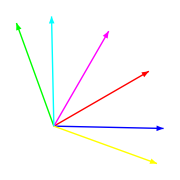
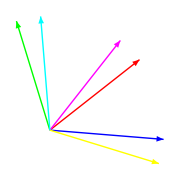
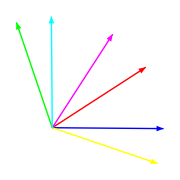
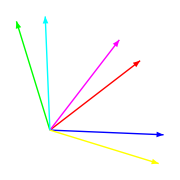
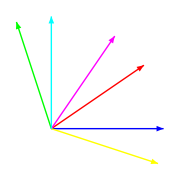
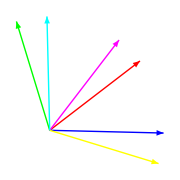

```mathematica
Table[drawAllVectors[all[[i,2]]],{i,Length[all]}]
```

```mathematica
(* PLOTTING THE QVALUERATIOS, ----------------------------------------------------,
i.e the quantum values for Subscript[x, 1]=1, Subscript[x, 2] variable, normalized by classical values *)
p05=PlotQvalues [5];
```

```mathematica
(* Try the following upper bound *)
trialBound[x_]:=√(1+x/4+x^2);
```

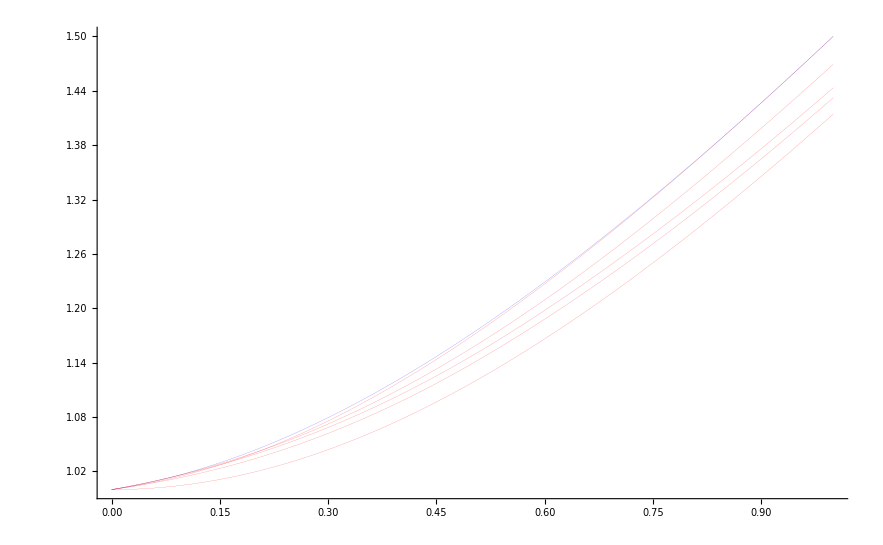

```mathematica
pb=Plot[trialBound[x],{x,0,1},PlotStyle->Directive[Thickness[.0001],Blue]];
Show[p05,pb]
```

```mathematica
(* Clear that if one SV is 1 and the second is nonzero, then you can violate the classical case. *)
(* Interestingly, seems only first order has zero derivative at Subscript[x, 2]=0, and the others all have about the same derivative .... their graphical shape is similar - seems order 2 does provide the highest bound, except potentially in the beginning of the graph - but that last point may just be due to numerical errors at small values *)
```

```mathematica
(* ratios for all orders very close so constraints all very close, but I know for order 1 it is Subscript[x, 1]^2+Subscript[x, 2]^2≤1, and order 2 it is probably Subscript[x, 1]^2+Subscript[x, 1] Subscript[x, 2]/4+Subscript[x, 2]^2≤1, so may be the small difference is just the extra term .. this is unclear and needs exploration *)
```

```mathematica
(* it turns out a fairly close upper bound, but seems the actual bound is not a simple function *)
```

```mathematica
(* ----------------------------------------------------------------------------------------------,  STEP BY STEP TESTING OF THE FUNCTIONS IN THE FILE 
Collected these from the "development phase" after each function .. remove semicolon in end to see result

par=partitions2[{1,2,3,4}];
(* test number of partitions is equal to "double factorial" or odd number factorial ... only works up to 10, for 12 recursion limit is reached *)
Table[{Length[partitions2[Range[i]]],(i-1)!!},{i,2,10,2}];

(* test that get coeff equals the brute force method *)
vecs={RUV,RUV,RUV,RUV};
inp=vecs.vecsᵀ;
vecs[[1]].vecs[[2]] vecs[[3]].vecs[[4]] + vecs[[1]].vecs[[3]] vecs[[2]].vecs[[4]] + vecs[[1]].vecs[[4]] vecs[[3]].vecs[[2]] ;
getcoeff[inp,par];

SupVecIndices[3];

a={RUV,RUV,RUV,RUV};
Table[symProd[a,a.aᵀ,SupVecIndices[3][[i]]],{i,8}];
A=SuperVector[a];

(a[[1]].a[[2]] a[[4]] + a[[1]].a[[4]] a[[2]] + a[[2]].a[[4]] a[[1]])/3;

Qvalue[A,A,dm[{1,1,1}]];

findQvalue[a,b,Σ];

g5=getMax[{1,1,1},5,1]; *)
```

```mathematica
(* For Singlet state explicitly *)
singlet=FullSeries[-{1,1,1},3]
```

(1.414 | (-0.924 | 0.383 | 0.
0.383 | 0.924 | 0.) | (1. | 0.
0. | 1.) | (0.383 | -0.924 | 0.
0.924 | 0.383 | 0.) | (1. | 0.
0. | 1.) | (-0.707 | -0.707
-0.707 | 0.707)
1.5 | (-0.707 | 0.707 | 0.
-0.966 | -0.259 | 0.
0.259 | 0.966 | 0.) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (0.707 | -0.707 | 0.
-0.259 | -0.966 | 0.
0.966 | 0.259 | 0.) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (-1. | -0.5 | -0.5
-0.5 | 0.5 | -1.
-0.5 | -1. | 0.5)
1.432 | (0.541 | -0.747 | 0.387
0.896 | 0.212 | -0.391
0.041 | -0.819 | 0.573
0.041 | -0.819 | 0.573) | (1. | 0.175 | 0.855 | 0.855
0.175 | 1. | -0.36 | -0.36
0.855 | -0.36 | 1. | 1.
0.855 | -0.36 | 1. | 1.) | (-0.875 | 0.472 | -0.103
0.274 | 0.747 | -0.606
-0.974 | 0.055 | 0.221
-0.974 | 0.055 | 0.221) | (1. | 0.175 | 0.855 | 0.855
0.175 | 1. | -0.36 | -0.36
0.855 | -0.36 | 1. | 1.
0.855 | -0.36 | 1. | 1.) | (-0.866 | -0.644 | -0.481 | -0.481
-0.644 | 0.641 | -0.947 | -0.947
-0.481 | -0.947 | 0.042 | 0.042
-0.481 | -0.947 | 0.042 | 0.042))

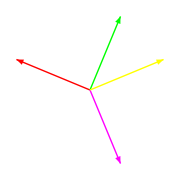
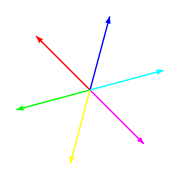
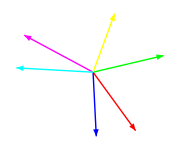

```mathematica
drawAllVectors[%]
```

```mathematica
(* With normalized product vectors in symProd function above ... get nonsensical results beyond 2, meaning Werner model not applicable .. may even not be bounded ... this method is arbitrary just to make sure eigenvalues +/-1, but has no operator significance *)
```

```mathematica
FullSeries[{1,1,0},7]
```

(1.414 | (0.924 | 0.383 | 0.
-0.383 | 0.924 | 0.) | (1. | 0.
0. | 1.) | (0.383 | 0.924 | 0.
0.924 | -0.383 | 0.) | (1. | 0.
0. | 1.) | (0.707 | 0.707
0.707 | -0.707)
1.75 | (0.706 | 0.708 | 0.
-0.261 | 0.965 | 0.
0.966 | -0.257 | 0.) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (0.71 | 0.704 | -0.001
0.965 | -0.263 | 0.
-0.255 | 0.967 | -0.001) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (1. | 0.495 | 0.505
0.495 | -0.505 | 1.
0.505 | 1. | -0.495)
1.459 | (0.987 | 0.16 | 0.
-0.533 | 0.846 | 0.
0.958 | 0.288 | 0.
0.958 | 0.288 | 0.) | (1. | -0.39 | 0.991 | 0.991
-0.39 | 1. | -0.266 | -0.266
0.991 | -0.266 | 1. | 1.
0.991 | -0.266 | 1. | 1.) | (0.16 | 0.987 | 0.
0.846 | -0.533 | 0.
0.288 | 0.958 | 0.
0.288 | 0.958 | 0.) | (1. | -0.39 | 0.991 | 0.991
-0.39 | 1. | -0.266 | -0.266
0.991 | -0.266 | 1. | 1.
0.991 | -0.266 | 1. | 1.) | (0.316 | 0.75 | 0.438 | 0.438
0.75 | -0.902 | 0.657 | 0.657
0.438 | 0.657 | 0.552 | 0.552
0.438 | 0.657 | 0.552 | 0.552)
2.029 | (0.999 | 0.023 | -0.034
-0.519 | 0.854 | 0.035
0.48 | 0.877 | 0.001
0.999 | 0.023 | -0.034
0.522 | -0.852 | -0.034) | (1. | -0.5 | 0.5 | 1. | 0.503
-0.5 | 1. | 0.5 | -0.5 | -1.
0.5 | 0.5 | 1. | 0.5 | -0.497
1. | -0.5 | 0.5 | 1. | 0.503
0.503 | -1. | -0.497 | 0.503 | 1.) | (-0.293 | 0.954 | 0.068
0.972 | -0.229 | -0.057
-0.229 | 0.973 | 0.032
-0.283 | 0.957 | 0.066
0.688 | 0.726 | 0.009) | (1. | -0.507 | 0.997 | 1. | 0.491
-0.507 | 1. | -0.448 | -0.498 | 0.502
0.997 | -0.448 | 1. | 0.998 | 0.548
1. | -0.498 | 0.998 | 1. | 0.5
0.491 | 0.502 | 0.548 | 0.5 | 1.) | (-0.273 | 0.968 | -0.208 | -0.263 | 0.704
0.969 | -0.702 | 0.951 | 0.967 | 0.263
0.696 | 0.266 | 0.743 | 0.703 | 0.967
-0.273 | 0.968 | -0.208 | -0.263 | 0.704
-0.968 | 0.704 | -0.95 | -0.966 | -0.26)
1.525 | (1. | 0.015 | 0.
-0.556 | 0.831 | 0.
0.931 | 0.365 | 0.
0.931 | 0.365 | 0.
0.931 | 0.365 | 0.
0.931 | 0.365 | 0.) | (1. | -0.543 | 0.937 | 0.937 | 0.937 | 0.937
-0.543 | 1. | -0.214 | -0.214 | -0.214 | -0.214
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.) | (0.015 | 1. | 0.
0.831 | -0.556 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.) | (1. | -0.543 | 0.937 | 0.937 | 0.937 | 0.937
-0.543 | 1. | -0.214 | -0.214 | -0.214 | -0.214
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.) | (0.031 | 0.823 | 0.379 | 0.379 | 0.379 | 0.379
0.823 | -0.924 | 0.572 | 0.572 | 0.572 | 0.572
0.379 | 0.572 | 0.679 | 0.679 | 0.679 | 0.679
0.379 | 0.572 | 0.679 | 0.679 | 0.679 | 0.679
0.379 | 0.572 | 0.679 | 0.679 | 0.679 | 0.679
0.379 | 0.572 | 0.679 | 0.679 | 0.679 | 0.679)
1.553 | (0.999 | -0.041 | 0.
-0.556 | 0.831 | 0.
0.918 | 0.396 | 0.
0.918 | 0.396 | 0.
0.918 | 0.396 | 0.
0.918 | 0.396 | 0.
0.918 | 0.396 | 0.) | (1. | -0.589 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901
-0.589 | 1. | -0.182 | -0.182 | -0.182 | -0.182 | -0.182
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.) | (-0.041 | 0.999 | 0.
0.831 | -0.556 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.) | (1. | -0.589 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901
-0.589 | 1. | -0.182 | -0.182 | -0.182 | -0.182 | -0.182
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.) | (-0.082 | 0.853 | 0.358 | 0.358 | 0.358 | 0.358 | 0.358
0.853 | -0.924 | 0.544 | 0.544 | 0.544 | 0.544 | 0.544
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727)
1.573 | (0.998 | -0.059 | 0.
-0.554 | 0.833 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.) | (1. | -0.602 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901
-0.602 | 1. | -0.196 | -0.196 | -0.196 | -0.196 | -0.196 | -0.196
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.) | (-0.059 | 0.998 | 0.
0.833 | -0.554 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.) | (1. | -0.602 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901
-0.602 | 1. | -0.196 | -0.196 | -0.196 | -0.196 | -0.196 | -0.196
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.) | (-0.118 | 0.864 | 0.325 | 0.325 | 0.325 | 0.325 | 0.325 | 0.325
0.864 | -0.922 | 0.559 | 0.559 | 0.559 | 0.559 | 0.559 | 0.559
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703))

```mathematica
FullSeries[{1,1,1},7]
```

(1.414 | (0.924 | 0.383 | 0.
-0.383 | 0.924 | 0.) | (1. | 0.
0. | 1.) | (0.383 | 0.924 | 0.
0.924 | -0.383 | 0.) | (1. | 0.
0. | 1.) | (0.707 | 0.707
0.707 | -0.707)
1.75 | (0.706 | 0.708 | -0.001
-0.26 | 0.966 | 0.
0.966 | -0.257 | 0.) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (0.709 | 0.705 | 0.001
0.965 | -0.261 | 0.001
-0.256 | 0.967 | 0.001) | (1. | 0.5 | 0.5
0.5 | 1. | -0.5
0.5 | -0.5 | 1.) | (1. | 0.497 | 0.504
0.497 | -0.503 | 1.
0.504 | 1. | -0.496)
1.459 | (0.987 | 0.16 | 0.
-0.533 | 0.846 | 0.
0.958 | 0.288 | 0.
0.958 | 0.288 | 0.) | (1. | -0.39 | 0.991 | 0.991
-0.39 | 1. | -0.266 | -0.266
0.991 | -0.266 | 1. | 1.
0.991 | -0.266 | 1. | 1.) | (0.16 | 0.987 | 0.
0.846 | -0.533 | 0.
0.288 | 0.958 | 0.
0.288 | 0.958 | 0.) | (1. | -0.39 | 0.991 | 0.991
-0.39 | 1. | -0.266 | -0.266
0.991 | -0.266 | 1. | 1.
0.991 | -0.266 | 1. | 1.) | (0.316 | 0.75 | 0.438 | 0.438
0.75 | -0.902 | 0.657 | 0.657
0.438 | 0.657 | 0.552 | 0.552
0.438 | 0.657 | 0.552 | 0.552)
2.726 | (-0.069 | -0.571 | -0.818
-0.413 | 0.893 | 0.178
0.789 | -0.311 | 0.53
0.488 | 0.754 | -0.441
0.402 | 0.59 | 0.701) | (1. | -0.627 | -0.31 | -0.103 | -0.937
-0.627 | 1. | -0.51 | 0.393 | 0.485
-0.31 | -0.51 | 1. | -0.082 | 0.505
-0.103 | 0.393 | -0.082 | 1. | 0.332
-0.937 | 0.485 | 0.505 | 0.332 | 1.) | (-0.472 | 0.645 | -0.601
0.877 | -0.333 | -0.345
0.714 | 0.479 | 0.51
-0.854 | 0.474 | -0.213
0.064 | 0.919 | 0.39) | (1. | -0.422 | -0.334 | 0.837 | 0.328
-0.422 | 1. | 0.291 | -0.834 | -0.385
-0.334 | 0.291 | 1. | -0.492 | 0.685
0.837 | -0.834 | -0.492 | 1. | 0.297
0.328 | -0.385 | 0.685 | 0.297 | 1.) | (0.155 | 0.413 | -0.74 | -0.037 | -0.848
0.665 | -0.722 | 0.223 | 0.738 | 0.863
-0.891 | 0.613 | 0.685 | -0.935 | -0.028
0.521 | 0.329 | 0.485 | 0.034 | 0.552
-0.23 | -0.086 | 0.927 | -0.213 | 0.841)
1.525 | (1. | 0.015 | 0.
-0.556 | 0.831 | 0.
0.931 | 0.365 | 0.
0.931 | 0.365 | 0.
0.931 | 0.365 | 0.
0.931 | 0.365 | 0.) | (1. | -0.543 | 0.937 | 0.937 | 0.937 | 0.937
-0.543 | 1. | -0.214 | -0.214 | -0.214 | -0.214
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.) | (0.015 | 1. | 0.
0.831 | -0.556 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.
0.365 | 0.931 | 0.) | (1. | -0.543 | 0.937 | 0.937 | 0.937 | 0.937
-0.543 | 1. | -0.214 | -0.214 | -0.214 | -0.214
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.
0.937 | -0.214 | 1. | 1. | 1. | 1.) | (0.031 | 0.823 | 0.379 | 0.379 | 0.379 | 0.379
0.823 | -0.924 | 0.572 | 0.572 | 0.572 | 0.572
0.379 | 0.572 | 0.679 | 0.679 | 0.679 | 0.679
0.379 | 0.572 | 0.679 | 0.679 | 0.679 | 0.679
0.379 | 0.572 | 0.679 | 0.679 | 0.679 | 0.679
0.379 | 0.572 | 0.679 | 0.679 | 0.679 | 0.679)
1.553 | (0.999 | -0.041 | 0.
-0.556 | 0.831 | 0.
0.918 | 0.396 | 0.
0.918 | 0.396 | 0.
0.918 | 0.396 | 0.
0.918 | 0.396 | 0.
0.918 | 0.396 | 0.) | (1. | -0.589 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901
-0.589 | 1. | -0.182 | -0.182 | -0.182 | -0.182 | -0.182
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.) | (-0.041 | 0.999 | 0.
0.831 | -0.556 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.
0.396 | 0.918 | 0.) | (1. | -0.589 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901
-0.589 | 1. | -0.182 | -0.182 | -0.182 | -0.182 | -0.182
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.
0.901 | -0.182 | 1. | 1. | 1. | 1. | 1.) | (-0.082 | 0.853 | 0.358 | 0.358 | 0.358 | 0.358 | 0.358
0.853 | -0.924 | 0.544 | 0.544 | 0.544 | 0.544 | 0.544
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727
0.358 | 0.544 | 0.727 | 0.727 | 0.727 | 0.727 | 0.727)
1.573 | (0.998 | -0.059 | 0.
-0.554 | 0.833 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.
0.925 | 0.38 | 0.) | (1. | -0.602 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901
-0.602 | 1. | -0.196 | -0.196 | -0.196 | -0.196 | -0.196 | -0.196
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.) | (-0.059 | 0.998 | 0.
0.833 | -0.554 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.
0.38 | 0.925 | 0.) | (1. | -0.602 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901 | 0.901
-0.602 | 1. | -0.196 | -0.196 | -0.196 | -0.196 | -0.196 | -0.196
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.
0.901 | -0.196 | 1. | 1. | 1. | 1. | 1. | 1.) | (-0.118 | 0.864 | 0.325 | 0.325 | 0.325 | 0.325 | 0.325 | 0.325
0.864 | -0.922 | 0.559 | 0.559 | 0.559 | 0.559 | 0.559 | 0.559
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703
0.325 | 0.559 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703 | 0.703))